# Physics 230 -- Lab 8 (Data Processing)

## Learning Outcomes 1. Understand how Mathematica handles units associated with data. 2. Load data from files and from internet sources. 3. Manipulate data structures in Mathematica.

Begin by watching this introductory video about data processing in Mathematica.

Most scientists spend a great deal of time working with data.  In this lab, we will introduce some important tools for importing and exporting a variety of data types to and from Mathematica, and will also practice the art of manipulating complicated multidimensional lists (i.e. arrays) of data.

```mathematica
Clear["`*" ]
SetDirectory[NotebookDirectory[]]    (* this command is explained below, but given here for your reference *)
```

## Units, Packages, System Variables

### Units

One useful Mathematica feature for physics students is the ability to use and calculate with physical units. See for example, this Units Overview Tutorial. Values with a magnitude and dimension can be defined using the Quantity command.

```mathematica
position = Quantity[12,"Meters"]
time = Quantity[5,"Seconds"]
vel = position/time //N
```

You can also add units via control-equals, which activates a connection to Wolfram Alpha and allows for a bit more flexibility in spelling of units. I myself find that it’s the easiest way to add units. To get the odd looking thing in the next box, I typed “length1=” then “control-equals” (to activate Wolfram Alpha parsing), then “14.3 km”.

```mathematica
length1=LinguisticAssistant
```

Try typing something with units via a control-equals on your own, so you can see how it works. For example, type “length2=” then “control-equals” then “14.3 kilomeaters”  (a deliberate misspelling which Wolfram Alpha should be able to handle).

```mathematica
(* empty box for you to use *)
length2=LinguisticAssistant
```

14.3 km

Many physical constants (with their units) are built into Mathematica. For example:

```mathematica
h=Quantity["PlanckConstant"]
h=LinguisticAssistant   (* same thing, using control-equals and "plank's constant" after the equals sign *)
k=Quantity["BoltzmannConstant"]
k=LinguisticAssistant (* same thing, using control-equals and "boltzmann's constant" after the equals sign *)
c=Quantity["SpeedOfLight"]
c=LinguisticAssistant (* same thing, using control-equals and "speed of light" after the equals sign *)
```

The UnitConvert function allows you to convert units:

```mathematica
UnitConvert[length1,"Cubits"] //N
UnitConvert[c,"Feet"/"Nanoseconds"] //N   (* Notice the "divided by" symbol as part of the argument.*)  (* and notice that the speed of light is almost exactly 1 foot per nanosecond *)
```

Mathematica can do more with units than just simple conversion. Here’s an example where I’m calculating (a) the current gravitational force between the earth and the moon, and (b) the amount of energy it would take to move the moon 1000x farther away from the earth (using the work from point a to point b=∫_a^b Fⅆx).

```mathematica
(* part a *)
G =LinguisticAssistant ;
me=AstronomicalData["Earth", "Mass"]  ;
mm = AstronomicalData["Moon", "Mass"]  ;
startingdistance=LinguisticAssistant ; (* to get this line I typed "startingdistance =" <control-equals> "distance from earth to the moon" *)
currentforce = G me mm/startingdistance^2 ;
UnitConvert[%, "Newtons"]
(* part b *)
force[x_] =  -G me mm/x^2;
energytomovemoon = -Integrate[force[x],{x,startingdistance,1000 startingdistance}]; (* negative sign because the force to move the earth is opposing the force of gravity *)
UnitConvert[energytomovemoon, "Joules"]
```

### Built-in functions

As you know, Mathematica has many, many, built-in functions. You can use the command Names to see them. There are thousands of built-in functions, so let’s just look at all of the Mathematica functions and symbols that start with a "W".

```mathematica
Names["W*"]
```

{WaitAll,WaitAsynchronousTask,WaitNext,WaitUntil,WakebyDistribution,WalleniusHypergeometricDistribution,WaringYuleDistribution,WarpingCorrespondence,WarpingDistance,WatershedComponents,WatsonUSquareTest,WattsStrogatzGraphDistribution,WaveletBestBasis,WaveletFilterCoefficients,WaveletImagePlot,WaveletListPlot,WaveletMapIndexed,WaveletMatrixPlot,WaveletPhi,WaveletPsi,WaveletScale,WaveletScalogram,WaveletThreshold,WeaklyConnectedComponents,WeaklyConnectedGraphComponents,WeaklyConnectedGraphQ,WeakStationarity,WeatherData,WeatherForecastData,WebAudioSearch,WebElementObject,WeberE,WebExecute,WebImage,WebImageSearch,WebPageMetaInformation,WebSearch,WebSessionObject,WebSessions,WebWindowObject,Wedge,Wednesday,WeibullDistribution,WeierstrassE1,WeierstrassE2,WeierstrassE3,WeierstrassEta1,WeierstrassEta2,WeierstrassEta3,WeierstrassHalfPeriods,WeierstrassHalfPeriodW1,WeierstrassHalfPeriodW2,WeierstrassHalfPeriodW3,WeierstrassInvariantG2,WeierstrassInvariantG3,WeierstrassInvariants,WeierstrassP,WeierstrassPPrime,WeierstrassSigma,WeierstrassZeta,WeightedAdjacencyGraph,WeightedAdjacencyMatrix,WeightedData,WeightedGraphQ,Weights,WelchWindow,WheelGraph,WhenEvent,Which,While,White,WhiteNoiseProcess,WhitePoint,Whitespace,WhitespaceCharacter,WhittakerM,WhittakerW,WienerFilter,WienerProcess,WignerD,WignerSemicircleDistribution,WikidataData,WikidataSearch,WikipediaData,WikipediaSearch,WilksW,WilksWTest,WindDirectionData,WindingCount,WindingPolygon,WindowClickSelect,WindowElements,WindowFloating,WindowFrame,WindowFrameElements,WindowMargins,WindowMovable,WindowOpacity,WindowPersistentStyles,WindowSelected,WindowSize,WindowStatusArea,WindowTitle,WindowToolbars,WindowWidth,WindSpeedData,WindVectorData,WinsorizedMean,WinsorizedVariance,WishartMatrixDistribution,With,WolframAlpha,WolframAlphaDate,WolframAlphaQuantity,WolframAlphaResult,WolframLanguageData,Word,WordBoundary,WordCharacter,WordCloud,WordCount,WordCounts,WordData,WordDefinition,WordFrequency,WordFrequencyData,WordList,WordOrientation,WordSearch,WordSelectionFunction,WordSeparators,WordSpacings,WordStem,WordTranslation,WorkingPrecision,WrapAround,Write,WriteLine,WriteString,Wronskian}

Here’s a way to see how many built-in functions there are. (Any functions or variables you’ve defined yourself will be included in the number.)

```mathematica
startupnames = Names["*"];
Length[startupnames]
```

### Packages

Packages are a way to enhance Mathematica’s capability by loading in additional commands for you to use. Loading a package is done with the Get command (shortcut <<), or with the very similar  Needs command, with a  `  after the package name to signify that the package is to be loaded into the current session:  

<<PackageName`

or 

Needs[“PackageName`”]

The Standard Extra Packages available in Mathematica 9.0 are listed in the listed in the Documentation Center. Typically you may run across a package when searching Help for a specific command or topic. For example, I discovered that Mathematica has built-in commands for working with resonance lines in atomic spectra. This is the Resonance Absorption Lines Package. The first input line of the help file says:  

<<ResonanceAbsorptionLines`

That’s a giveaway that the things discussed in this particular help file are not part of the standard Mathematica functionality, but rather new functions will become available after you load the relevant package (the “Resonance Absorption Lines” package, in this case). Evaluate the cell below to see the new functions and symbols defined after loading the ResonanceAbsorptionLines package. (Note the neat trick using Complement to see which commands currently loaded were not part of the startupnames variable defined above.)

```mathematica
<<ResonanceAbsorptionLines`
currentnames = Names["*"];
Length[currentnames]  (* includes additional functions loaded via the package *)

newnames = Complement[currentnames,startupnames]
Length[newnames]  (* how many new ones there are *)
```

7091

Complement::normal: Nonatomic expression expected at position 2 in Complement[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,«7041»},startupnames].

Complement[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,Ξ,Ο,Π,Ρ,Σ,Τ,Υ,Φ,Χ,Ψ,Ω,α,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,ς,σ,τ,υ,φ,χ,ψ,ω,ϑ,ϒ,ϕ,ϖ,Ϛ,ϛ,Ϝ,ϝ,Ϟ,ϟ,Ϡ,ϡ,ϰ,ϱ,ϵ,AASTriangle,Abampere,Abcoulomb,AbelianGroup,Abfarad,Abhenry,Abmho,Abohm,Abort,AbortKernels,AbortProtect,AbortScheduledTask,Above,Abs,AbsArg,AbsArgPlot,Absolute,AbsoluteCorrelation,AbsoluteCorrelationFunction,AbsoluteCurrentValue,AbsoluteDashing,AbsoluteFileName,AbsoluteOptions,AbsolutePointSize,AbsoluteThickness,AbsoluteTime,AbsoluteTiming,Abvolt,AcceptanceThreshold,AccountingForm,Accumulate,Accuracy,AccuracyGoal,Acre,ActionDelay,ActionMenu,ActionMenuBox,ActionMenuBoxOptions,Activate,Active,ActiveClassification,ActiveClassificationObject,ActiveItem,ActivePrediction,ActivePredictionObject,ActiveStyle,AcyclicGraphQ,AddDocumentationDirectory,AddDocumentationNotebook,AddOnHelpPath,AddSides,AddTo,AddToSearchIndex,AddUsers,AdjacencyGraph,AdjacencyList,AdjacencyMatrix,AdjacentMeshCells,AdjustmentBox,AdjustmentBoxOptions,AdjustTimeSeriesForecast,AdministrativeDivisionData,AffineHalfSpace,AffineSpace,AffineStateSpaceModel,AffineTransform,After,AggregatedEntityClass,AggregationLayer,AircraftData,AirportData,AirPressureData,AirTemperatureData,AirWavelength,AiryAi,AiryAiPrime,AiryAiZero,AiryBi,AiryBiPrime,AiryBiZero,AlgebraicIntegerQ,AlgebraicNumber,AlgebraicNumberDenominator,AlgebraicNumberNorm,AlgebraicNumberPolynomial,AlgebraicNumberTrace,AlgebraicRules,AlgebraicRulesData,Algebraics,AlgebraicUnitQ,Alignment,AlignmentMarker,AlignmentPoint,All,AllowAdultContent,AllowedCloudExtraParameters,AllowedCloudParameterExtensions,AllowedDimensions,AllowedFrequencyRange,AllowedHeads,AllowGroupClose,AllowIncomplete,AllowInlineCells,AllowKernelInitialization,AllowLooseGrammar,AllowReverseGroupClose,AllowScriptLevelChange,AllowVersionUpdate,AllTrue,Alphabet,AlphabeticOrder,AlphabeticSort,AlphaChannel,AlternateImage,AlternatingFactorial,AlternatingGroup,AlternativeHypothesis,Alternatives,AltitudeMethod,AmbientLight,AmbiguityFunction,AmbiguityList,Amp,Ampere,AMU,Analytic,AnatomyData,AnatomyForm,AnatomyPlot3D,AnatomySkinStyle,AnatomyStyling,AnchoredSearch,And,AndersonDarlingTest,AngerJ,AngleBisector,AngleBracket,AnglePath,AnglePath3D,AngleVector,Angstrom,AngularGauge,Animate,AnimationCycleOffset,AnimationCycleRepetitions,AnimationDirection,AnimationDisplayTime,AnimationRate,AnimationRepetitions,AnimationRunning,AnimationRunTime,AnimationTimeIndex,Animator,AnimatorBox,AnimatorBoxOptions,AnimatorElements,Annotate,Annotation,AnnotationDelete,AnnotationKeys,AnnotationRules,AnnotationValue,Annuity,AnnuityDue,Annulus,AnomalyDetection,AnomalyDetector,AnomalyDetectorFunction,Anonymous,Antialiasing,AntihermitianMatrixQ,Antisymmetric,AntisymmetricMatrixQ,Antonyms,AnyOrder,AnySubset,AnyTrue,Apart,ApartSquareFree,APIFunction,Apostilb,Appearance,AppearanceElements,AppearanceRules,AppellF1,Append,AppendCheck,AppendLayer,AppendTo,ApplicationAdd,ApplicationDataDirectory,ApplicationDataUserDirectory,ApplicationDirectoriesLocate,ApplicationDirectoryAdd,ApplicationsLocate,Apply,ApplySides,ArcCos,ArcCosh,ArcCot,ArcCoth,ArcCsc,ArcCsch,ArcCurvature,ARCHProcess,ArcLength,ArcMinute,ArcSec,ArcSech,ArcSecond,ArcSin,ArcSinDistribution,ArcSinh,ArcTan,ArcTanh,Are,Area,Arg,ArgMax,ArgMin,ArgumentCountQ,ARIMAProcess,ArithmeticGeometricMean,ARMAProcess,Around,AroundReplace,ARProcess,Array,ArrayComponents,ArrayDepth,ArrayFilter,ArrayFlatten,ArrayMesh,ArrayPad,ArrayPlot,ArrayQ,ArrayResample,ArrayReshape,ArrayRules,Arrays,Arrow,Arrow3DBox,ArrowBox,Arrowheads,ASATriangle,Ask,AskAppend,AskConfirm,AskDisplay,AskedQ,AskedValue,AskFunction,AskState,AskTemplateDisplay,AspectRatio,AspectRatioFixed,AssayTon,Assert,AssociateTo,Association,AssociationFormat,AssociationMap,AssociationQ,AssociationThread,AssumeDeterministic,Assuming,Assumptions,AstronomicalData,AstronomicalUnit,Asymptotic,AsymptoticDSolveValue,AsymptoticEqual,AsymptoticEquivalent,AsymptoticGreater,AsymptoticGreaterEqual,AsymptoticIntegrate,AsymptoticLess,AsymptoticLessEqual,AsymptoticOutputTracker,AsymptoticProduct,AsymptoticRSolveValue,AsymptoticSolve,AsymptoticSum,Asynchronous,AsynchronousTaskObject,AsynchronousTasks,Atmosphere,Atom,AtomCoordinates,AtomCount,AtomDiagramCoordinates,AtomicData,AtomicMassUnit,AtomList,AtomQ,AttentionLayer,Atto,Attributes,AU,Audio,AudioAmplify,AudioAnnotate,AudioAnnotationLookup,AudioBlockMap,AudioCapture,AudioChannelAssignment,AudioChannelCombine,AudioChannelMix,AudioChannels,AudioChannelSeparate,AudioData,AudioDelay,AudioDelete,AudioDevice,AudioDistance,AudioEncoding,AudioFade,AudioFrequencyShift,AudioGenerator,AudioIdentify,AudioInputDevice,AudioInsert,AudioInstanceQ,AudioIntervals,AudioJoin,AudioLabel,AudioLength,AudioLocalMeasurements,AudioLooping,AudioLoudness,AudioMeasurements,AudioNormalize,AudioOutputDevice,AudioOverlay,AudioPad,AudioPan,AudioPartition,AudioPause,AudioPitchShift,AudioPlay,AudioPlot,AudioQ,AudioRecord,AudioReplace,AudioResample,AudioReverb,AudioReverse,AudioSampleRate,AudioSpectralMap,AudioSpectralTransformation,AudioSplit,AudioStop,AudioStream,AudioStreams,AudioTimeStretch,AudioTracks,AudioTrim,AudioType,AugmentedPolyhedron,AugmentedSymmetricPolynomial,Authenticate,Authentication,AuthenticationDialog,AutoAction,Autocomplete,AutocompletionFunction,AutoCopy,AutocorrelationTest,AutoDelete,AutoEvaluateEvents,AutoGeneratedPackage,AutoIndent,AutoIndentSpacings,AutoItalicWords,AutoloadPath,AutoMatch,Automatic,AutomaticImageSize,AutoMultiplicationSymbol,AutoNumberFormatting,AutoOpenNotebooks,AutoOpenPalettes,AutoQuoteCharacters,AutoRefreshed,AutoRemove,AutorunSequencing,AutoScaling,AutoScroll,AutoSpacing,AutoStyleOptions,AutoStyleWords,AutoSubmitting,AvoirdupoisOunce,AvoirdupoisPound,Axes,AxesEdge,AxesLabel,AxesOrigin,AxesStyle,AxiomaticTheory,Axis,BabyMonsterGroupB,Back,Background,BackgroundAppearance,BackgroundTasksSettings,Backslash,Backsubstitution,Backward,Bag,BakersDozen,Bale,Ball,Band,BandpassFilter,BandstopFilter,Bar,BarabasiAlbertGraphDistribution,BarChart,BarChart3D,BarcodeImage,BarcodeRecognize,BaringhausHenzeTest,BarLegend,BarlowProschanImportance,Barn,BarnesG,BarOrigin,Barrel,BarSpacing,BartlettHannWindow,BartlettWindow,Barye,BaseDecode,BaseEncode,BaseForm,Baseline,BaselinePosition,BaseStyle,BasicRecurrentLayer,BatchNormalizationLayer,BatchSize,BatesDistribution,BattleLemarieWavelet,Baud,BayesianMaximization,BayesianMaximizationObject,BayesianMinimization,BayesianMinimizationObject,Because,BeckmannDistribution,Becquerel,Beep,Before,Begin,BeginDialogPacket,BeginFrontEndInteractionPacket,BeginPackage,BellB,BellY,Below,BenfordDistribution,BeniniDistribution,BenktanderGibratDistribution,BenktanderWeibullDistribution,BernoulliB,BernoulliDistribution,BernoulliGraphDistribution,BernoulliProcess,BernsteinBasis,BesselFilterModel,BesselI,BesselJ,BesselJZero,BesselK,BesselY,BesselYZero,Beta,BetaBinomialDistribution,BetaDistribution,BetaNegativeBinomialDistribution,BetaPrimeDistribution,BetaRegularized,Between,BetweennessCentrality,BeveledPolyhedron,BezierCurve,BezierCurve3DBox,BezierCurve3DBoxOptions,BezierCurveBox,BezierCurveBoxOptions,BezierFunction,BilateralFilter,Binarize,BinaryDeserialize,BinaryDistance,BinaryFormat,BinaryImageQ,BinaryRead,BinaryReadList,BinarySerialize,BinaryWrite,BinCounts,BinLists,Binomial,BinomialDistribution,BinomialProcess,BinormalDistribution,BiorthogonalSplineWavelet,Biot,BipartiteGraphQ,BiquadraticFilterModel,BirnbaumImportance,BirnbaumSaundersDistribution,Bit,BitAnd,BitClear,BitGet,BitLength,BitNot,BitOr,BitSet,BitShiftLeft,BitShiftRight,BitXor,BiweightLocation,BiweightMidvariance,Black,BlackmanHarrisWindow,BlackmanNuttallWindow,BlackmanWindow,Blank,BlankForm,BlankNullSequence,BlankSequence,Blend,Block,BlockchainAddressData,BlockchainBase,BlockchainBlockData,BlockchainContractValue,BlockchainData,BlockchainGet,BlockchainKeyEncode,BlockchainPut,BlockchainTokenData,BlockchainTransaction,BlockchainTransactionData,BlockchainTransactionSign,BlockchainTransactionSubmit,BlockMap,BlockRandom,BlomqvistBeta,BlomqvistBetaTest,Blue,Blur,BoardFoot,BodePlot,BohmanWindow,BohrMagneton,Bold,Bolt,Bond,BondCount,BondList,BondQ,Bookmarks,Boole,BooleanConsecutiveFunction,BooleanConvert,BooleanCountingFunction,BooleanFunction,BooleanGraph,BooleanMaxterms,BooleanMinimize,BooleanMinterms,BooleanQ,BooleanRegion,Booleans,BooleanStrings,BooleanTable,BooleanVariables,BorderDimensions,BorelTannerDistribution,Bottom,BottomHatTransform,BoundaryDiscretizeGraphics,BoundaryDiscretizeRegion,BoundaryMesh,BoundaryMeshRegion,BoundaryMeshRegionQ,BoundaryStyle,BoundedRegionQ,BoundingRegion,Bounds,Box,BoxBaselineShift,BoxData,BoxDimensions,Boxed,Boxes,BoxForm,BoxFormFormatTypes,BoxFrame,BoxID,BoxMargins,BoxMatrix,BoxObject,BoxRatios,BoxRotation,BoxRotationPoint,BoxStyle,BoxWhiskerChart,Bra,BracketingBar,BraKet,BrayCurtisDistance,BreadthFirstScan,Break,BridgeData,BrightnessEqualize,BritishThermalUnit,BroadcastStationData,Brown,BrownForsytheTest,BrownianBridgeProcess,BrowserCategory,BSplineBasis,BSplineCurve,BSplineCurve3DBox,BSplineCurve3DBoxOptions,BSplineCurveBox,BSplineCurveBoxOptions,BSplineFunction,BSplineSurface,BSplineSurface3DBox,BSplineSurface3DBoxOptions,BTU,BubbleChart,BubbleChart3D,BubbleScale,BubbleSizes,Bucket,BuildingData,BulletGauge,Bushel,BusinessDayQ,Butt,ButterflyGraph,ButterworthFilterModel,Button,ButtonBar,ButtonBox,ButtonBoxOptions,ButtonCell,ButtonContents,ButtonData,ButtonEvaluator,ButtonExpandable,ButtonFrame,ButtonFunction,ButtonMargins,ButtonMinHeight,ButtonNote,ButtonNotebook,ButtonSource,ButtonStyle,ButtonStyleMenuListing,Byte,ByteArray,ByteArrayFormat,ByteArrayQ,ByteArrayToString,ByteCount,ByteOrdering,C,Cable,CachedValue,CacheGraphics,CachePersistence,CalendarConvert,CalendarData,CalendarType,Caliber,Callout,CalloutMarker,CalloutStyle,CallPacket,Calorie,CanberraDistance,Cancel,CancelButton,Candela,Candle,CandlestickChart,CanonicalGraph,CanonicalizePolygon,CanonicalizePolyhedron,CanonicalName,CanonicalWarpingCorrespondence,CanonicalWarpingDistance,CantorMesh,CantorStaircase,Cap,CapForm,CapitalDifferentialD,Capitalize,CapsuleShape,CaptureRunning,Carat,CardinalBSplineBasis,CarlemanLinearize,CarmichaelLambda,CaseOrdering,Cases,CaseSensitive,Cashflow,Casoratian,Catalan,CatalanNumber,Catch,CategoricalDistribution,Catenate,CatenateLayer,CauchyDistribution,CauchyWindow,CayleyGraph,CDF,CDFDeploy,CDFInformation,CDFWavelet,Ceiling,CelestialSystem,Cell,CellAutoOverwrite,CellBaseline,CellBoundingBox,CellBracketOptions,CellChangeTimes,CellContents,CellContext,CellDingbat,CellDynamicExpression,CellEditDuplicate,CellElementsBoundingBox,CellElementSpacings,CellEpilog,CellEvaluationDuplicate,CellEvaluationFunction,CellEvaluationLanguage,CellEventActions,CellFrame,CellFrameColor,CellFrameLabelMargins,CellFrameLabels,CellFrameMargins,CellGroup,CellGroupData,CellGrouping,CellGroupingRules,CellHorizontalScrolling,CellID,CellLabel,CellLabelAutoDelete,CellLabelMargins,CellLabelPositioning,CellLabelStyle,CellLabelTemplate,CellMargins,CellObject,CellOpen,CellPrint,CellProlog,Cells,CellSize,CellStyle,CellTags,CellularAutomaton,Celsius,CensoredDistribution,Censoring,Cental,Center,CenterArray,CenterDot,Centi,Centigrade,Centimeter,CentralFeature,CentralMoment,CentralMomentGeneratingFunction,Century,Cepstrogram,CepstrogramArray,CepstrumArray,CForm,CGS,Chain,ChampernowneNumber,ChangeOptions,ChannelBase,ChannelBrokerAction,ChannelDatabin,ChannelHistoryLength,ChannelListen,ChannelListener,ChannelListeners,ChannelListenerWait,ChannelObject,ChannelPreSendFunction,ChannelReceiverFunction,ChannelSend,ChannelSubscribers,ChanVeseBinarize,Character,CharacterCounts,CharacterEncoding,CharacterEncodingsPath,CharacteristicFunction,CharacteristicPolynomial,CharacterName,CharacterNormalize,CharacterRange,Characters,ChartBaseStyle,ChartElementData,ChartElementDataFunction,ChartElementFunction,ChartElements,ChartLabels,ChartLayout,ChartLegends,ChartStyle,Chebyshev1FilterModel,Chebyshev2FilterModel,ChebyshevDistance,ChebyshevT,ChebyshevU,Check,CheckAbort,CheckAll,Checkbox,CheckboxBar,CheckboxBox,CheckboxBoxOptions,ChemicalData,ChessboardDistance,ChevalVapeur,ChiDistribution,ChineseRemainder,ChiSquareDistribution,ChoiceButtons,ChoiceDialog,CholeskyDecomposition,Chop,ChromaticityPlot,ChromaticityPlot3D,ChromaticPolynomial,Cicero,Circle,CircleBox,CircleDot,CircleMinus,CirclePlus,CirclePoints,CircleThrough,CircleTimes,CirculantGraph,CircularOrthogonalMatrixDistribution,CircularQuaternionMatrixDistribution,CircularRealMatrixDistribution,CircularSymplecticMatrixDistribution,CircularUnitaryMatrixDistribution,Circumsphere,CityData,ClassifierFunction,ClassifierInformation,ClassifierMeasurements,ClassifierMeasurementsObject,Classify,ClassPriors,Clear,ClearAll,ClearAttributes,ClearCookies,ClearPermissions,ClearSystemCache,ClebschGordan,ClickPane,Clip,ClipboardNotebook,ClipFill,ClippingStyle,ClipPlanes,ClipPlanesStyle,ClipRange,Clock,ClockGauge,ClockwiseContourIntegral,Close,Closed,CloseDocumentationIndex,CloseDocumentationIndexMerger,CloseDocumentationNotebookIndexer,CloseKernels,ClosenessCentrality,Closing,ClosingAutoSave,ClosingEvent,CloudAccountData,CloudBase,CloudConnect,CloudConnections,CloudDeploy,CloudDirectory,CloudDisconnect,CloudEvaluate,CloudExport,CloudExpression,CloudExpressions,CloudFunction,CloudGet,CloudImport,CloudLoggingData,CloudObject,CloudObjectInformation,CloudObjectInformationData,CloudObjectNameFormat,CloudObjects,CloudObjectURLType,CloudPublish,CloudPut,CloudRenderingMethod,CloudSave,CloudShare,CloudSubmit,CloudSymbol,CloudUnshare,CloudUserID,ClusterClassify,ClusterDissimilarityFunction,ClusteringComponents,ClusteringTree,CMYKColor,Coarse,CodeAssistOptions,Coefficient,CoefficientArrays,CoefficientDomain,CoefficientList,CoefficientRules,CoifletWavelet,Collect,Colon,ColonForm,ColorBalance,ColorCombine,ColorConvert,ColorCoverage,ColorData,ColorDataFunction,ColorDetect,ColorDistance,ColorFunction,ColorFunctionScaling,Colorize,ColorNegate,ColorOutput,ColorProfileData,ColorQ,ColorQuantize,ColorReplace,ColorRules,ColorSelectorSettings,ColorSeparate,ColorSetter,ColorSetterBox,ColorSetterBoxOptions,ColorSlider,ColorsNear,ColorSpace,ColorToneMapping,Column,ColumnAlignments,ColumnBackgrounds,ColumnForm,ColumnLines,ColumnsEqual,ColumnSpacings,ColumnWidths,CombinedEntityClass,CombinerFunction,CometData,CommonDefaultFormatTypes,Commonest,CommonestFilter,CommonName,CommonUnits,CommunityBoundaryStyle,CommunityGraphPlot,CommunityLabels,CommunityRegionStyle,CompanyData,CompatibleUnitQ,CompilationOptions,CompilationTarget,Compile,Compiled,CompiledCodeFunction,CompiledFunction,CompilerOptions,Complement,ComplementedEntityClass,CompleteGraph,CompleteGraphQ,CompleteKaryTree,CompletionsListPacket,Complex,ComplexContourPlot,Complexes,ComplexExpand,ComplexInfinity,ComplexityFunction,ComplexListPlot,ComplexPlot,ComplexPlot3D,ComplexRegionPlot,ComplexStreamPlot,ComplexVectorPlot,ComponentMeasurements,ComponentwiseContextMenu,Compose,ComposeList,ComposeSeries,CompositeQ,Composition,CompoundElement,CompoundExpression,CompoundPoissonDistribution,CompoundPoissonProcess,CompoundRenewalProcess,Compress,CompressedData,CompressionLevel,ComputeUncertainty,Condition,ConditionalExpression,Conditioned,Cone,ConeBox,ConfidenceLevel,ConfidenceRange,ConfidenceTransform,ConfigurationPath,ConformAudio,ConformImages,Congruent,ConicHullRegion,ConicHullRegion3DBox,ConicHullRegionBox,ConicOptimization,Conjugate,ConjugateTranspose,Conjunction,Connect,ConnectedComponents,ConnectedGraphComponents,ConnectedGraphQ,ConnectedMeshComponents,ConnectedMoleculeComponents,ConnectedMoleculeQ,ConnectionSettings,ConnectLibraryCallbackFunction,ConnectSystemModelComponents,ConnesWindow,ConoverTest,ConsoleMessage,ConsoleMessagePacket,Constant,ConstantArray,ConstantArrayLayer,ConstantImage,ConstantPlusLayer,ConstantRegionQ,Constants,ConstantTimesLayer,ConstellationData,ConstrainedMax,ConstrainedMin,Construct,Containing,ContainsAll,ContainsAny,ContainsExactly,ContainsNone,ContainsOnly,ContentFieldOptions,ContentLocationFunction,ContentObject,ContentPadding,ContentsBoundingBox,ContentSelectable,ContentSize,Context,ContextMenu,Contexts,ContextToFileName,Continuation,Continue,ContinuedFraction,ContinuedFractionK,ContinuousAction,ContinuousMarkovProcess,ContinuousTask,ContinuousTimeModelQ,ContinuousWaveletData,ContinuousWaveletTransform,ContourDetect,ContourGraphics,ContourIntegral,ContourLabels,ContourLines,ContourPlot,ContourPlot3D,Contours,ContourShading,ContourSmoothing,ContourStyle,ContraharmonicMean,ContrastiveLossLayer,Control,ControlActive,ControlAlignment,ControlGroupContentsBox,ControllabilityGramian,ControllabilityMatrix,ControllableDecomposition,ControllableModelQ,ControllerDuration,ControllerInformation,ControllerInformationData,ControllerLinking,ControllerManipulate,ControllerMethod,ControllerPath,ControllerState,ControlPlacement,ControlsRendering,ControlType,Convergents,ConversionOptions,ConversionRules,Convert,ConvertTemperature,ConvertToBitmapPacket,ConvertToPostScript,ConvertToPostScriptPacket,ConvexHullMesh,ConvexPolygonQ,ConvexPolyhedronQ,ConvolutionLayer,Convolve,ConwayGroupCo1,ConwayGroupCo2,ConwayGroupCo3,CookieFunction,Cookies,CoordinateBoundingBox,CoordinateBoundingBoxArray,CoordinateBounds,CoordinateBoundsArray,CoordinateChartData,CoordinatesToolOptions,CoordinateTransform,CoordinateTransformData,CoprimeQ,Coproduct,CopulaDistribution,Copyable,CopyDatabin,CopyDirectory,CopyFile,CopyTag,CopyToClipboard,Cord,CornerFilter,CornerNeighbors,Correlation,CorrelationDistance,CorrelationFunction,CorrelationTest,Cos,Cosh,CoshIntegral,CosineDistance,CosineWindow,CosIntegral,Cot,Coth,Coulomb,Count,CountDistinct,CountDistinctBy,CounterAssignments,CounterBox,CounterBoxOptions,CounterClockwiseContourIntegral,CounterEvaluator,CounterFunction,CounterIncrements,CounterStyle,CounterStyleMenuListing,CountRoots,CountryData,Counts,CountsBy,Covariance,CovarianceEstimatorFunction,CovarianceFunction,CoxianDistribution,CoxIngersollRossProcess,CoxModel,CoxModelFit,CramerVonMisesTest,CreateArchive,CreateCellID,CreateChannel,CreateCloudExpression,CreateDatabin,CreateDataDirectory,CreateDataStructure,CreateDataSystemModel,CreateDialog,CreateDirectory,CreateDocument,CreateDocumentationIndex,CreateFile,CreateIntermediateDirectories,CreateManagedLibraryExpression,CreateNotebook,CreatePacletArchive,CreatePalette,CreatePalettePacket,CreatePermissionsGroup,CreateScheduledTask,CreateSearchIndex,CreateSpellIndex,CreateSystemModel,CreateTemporary,CreateUUID,CreateWindow,CriterionFunction,CriticalityFailureImportance,CriticalitySuccessImportance,CriticalSection,Cross,CrossEntropyLossLayer,CrossingCount,CrossingDetect,CrossingPolygon,CrossMatrix,Csc,Csch,CTCLossLayer,Cube,CubeRoot,Cubics,Cubit,Cuboid,CuboidBox,Cumulant,CumulantGeneratingFunction,Cup,CupCap,Curie,Curl,CurlyDoubleQuote,CurlyQuote,CurrencyConvert,CurrentDate,CurrentImage,CurrentlySpeakingPacket,currentnames,CurrentNotebookImage,CurrentScreenImage,CurrentValue,Curry,CurryApplied,CurvatureFlowFilter,CurveClosed,Cyan,CycleGraph,CycleIndexPolynomial,Cycles,CyclicGroup,Cyclotomic,Cylinder,CylinderBox,CylindricalDecomposition,D,DagumDistribution,Dalton,DamData,DamerauLevenshteinDistance,DampingConstant,DampingFactor,Darker,Dashed,Dashing,DatabaseConnect,DatabaseDisconnect,DatabaseReference,Databin,DatabinAdd,DatabinRemove,Databins,DatabinUpload,DataCompression,DataDistribution,DataRange,DataReversed,Dataset,DatasetDisplayPanel,DataStructure,DataStructureQ,Date,DateBounds,Dated,DateDelimiters,DateDifference,DatedUnit,DateFormat,DateFunction,DateHistogram,DateInterval,DateList,DateListLogPlot,DateListPlot,DateListStepPlot,DateObject,DateObjectQ,DateOverlapsQ,DatePattern,DatePlus,DateRange,DateReduction,DateString,DateTicksFormat,DateValue,DateWithinQ,DaubechiesWavelet,DavisDistribution,DawsonF,Day,DayCount,DayCountConvention,DayHemisphere,DaylightQ,DayMatchQ,DayName,DayNightTerminator,DayPlus,DayRange,DayRound,DeBruijnGraph,DeBruijnSequence,Debug,DebugTag,Deca,Decade,Decapitalize,Deci,Decimal,DecimalForm,DeclareKnownSymbols,DeclarePackage,Decompose,DeconvolutionLayer,Decrement,Decrypt,DecryptFile,DedekindEta,DeepSpaceProbeData,Default,DefaultAxesStyle,DefaultBaseStyle,DefaultBoxStyle,DefaultButton,DefaultColor,DefaultControlPlacement,DefaultDuplicateCellStyle,DefaultDuration,DefaultElement,DefaultFaceGridsStyle,DefaultFieldHintStyle,DefaultFont,DefaultFontProperties,DefaultFormatType,DefaultFormatTypeForStyle,DefaultFrameStyle,DefaultFrameTicksStyle,DefaultGridLinesStyle,DefaultInlineFormatType,DefaultInputFormatType,DefaultLabelStyle,DefaultMenuStyle,DefaultNaturalLanguage,DefaultNewCellStyle,DefaultNewInlineCellStyle,DefaultNotebook,DefaultOptions,DefaultOutputFormatType,DefaultPrintPrecision,DefaultStyle,DefaultStyleDefinitions,DefaultTextFormatType,DefaultTextInlineFormatType,DefaultTicksStyle,DefaultTooltipStyle,DefaultValue,DefaultValues,Defer,DefineExternal,DefineInputStreamMethod,DefineOutputStreamMethod,DefineResourceFunction,Definition,Degree,DegreeCentrality,DegreeGraphDistribution,DegreeLexicographic,DegreeReverseLexicographic,DEigensystem,DEigenvalues,Deinitialization,Del,DelaunayMesh,Delayed,Deletable,Delete,DeleteAnomalies,DeleteBorderComponents,DeleteCases,DeleteChannel,DeleteCloudExpression,DeleteContents,DeleteDirectory,DeleteDuplicates,DeleteDuplicatesBy,DeleteFile,DeleteMissing,DeleteObject,DeletePermissionsKey,DeleteSearchIndex,DeleteSmallComponents,DeleteStopwords,DeleteWithContents,DeletionWarning,DelimitedArray,DelimitedSequence,Delimiter,DelimiterFlashTime,DelimiterMatching,Delimiters,DeliveryFunction,Dendrogram,Denier,Denominator,DensityGraphics,DensityHistogram,DensityPlot,DensityPlot3D,DependentVariables,Deploy,Deployed,Depth,DepthFirstScan,Derivative,DerivativeFilter,DerivedKey,DescriptorStateSpace,DesignMatrix,DestroyAfterEvaluation,Det,Deuterium,DeviceClose,DeviceConfigure,DeviceExecute,DeviceExecuteAsynchronous,DeviceObject,DeviceOpen,DeviceOpenQ,DeviceRead,DeviceReadBuffer,DeviceReadLatest,DeviceReadList,DeviceReadTimeSeries,Devices,DeviceStreams,DeviceWrite,DeviceWriteBuffer,DGaussianWavelet,DiacriticalPositioning,Diagonal,DiagonalizableMatrixQ,DiagonalMatrix,DiagonalMatrixQ,Dialog,DialogIndent,DialogInput,DialogLevel,DialogNotebook,DialogProlog,DialogReturn,DialogSymbols,Diamond,DiamondMatrix,DiceDissimilarity,DictionaryLookup,DictionaryWordQ,Didot,DidotPoint,DifferenceDelta,DifferenceOrder,DifferenceQuotient,DifferenceRoot,DifferenceRootReduce,Differences,DifferentialD,DifferentialRoot,DifferentialRootReduce,DifferentiatorFilter,DigitalSignature,DigitBlock,DigitBlockMinimum,DigitCharacter,DigitCount,DigitQ,DihedralAngle,DihedralGroup,Dilation,DimensionalCombinations,DimensionalMeshComponents,DimensionReduce,DimensionReducerFunction,DimensionReduction,Dimensions,Diopter,DiracComb,DiracDelta,DirectedEdge,DirectedEdges,DirectedGraph,DirectedGraphQ,DirectedInfinity,DirectHitSearch,Direction,Directive,Directory,DirectoryName,DirectoryQ,DirectoryStack,DirichletBeta,DirichletCharacter,DirichletCondition,DirichletConvolve,DirichletDistribution,DirichletEta,DirichletL,DirichletLambda,DirichletTransform,DirichletWindow,DisableConsolePrintPacket,DisableFormatting,DiscreteAsymptotic,DiscreteChirpZTransform,DiscreteConvolve,DiscreteDelta,DiscreteHadamardTransform,DiscreteIndicator,DiscreteLimit,DiscreteLQEstimatorGains,DiscreteLQRegulatorGains,DiscreteLyapunovSolve,DiscreteMarkovProcess,DiscreteMaxLimit,DiscreteMinLimit,DiscretePlot,DiscretePlot3D,DiscreteRatio,DiscreteRiccatiSolve,DiscreteShift,DiscreteTimeModelQ,DiscreteUniformDistribution,DiscreteVariables,DiscreteWaveletData,DiscreteWaveletPacketTransform,DiscreteWaveletTransform,DiscretizeGraphics,DiscretizeRegion,Discriminant,DisjointQ,Disjunction,Disk,DiskBox,DiskMatrix,DiskSegment,Dispatch,DispatchQ,DispersionEstimatorFunction,Display,DisplayAllSteps,DisplayEndPacket,DisplayFlushImagePacket,DisplayForm,DisplayFunction,DisplayPacket,DisplayRules,DisplaySetSizePacket,DisplayString,DisplayTemporary,DisplayWith,DisplayWithRef,DisplayWithVariable,DistanceFunction,DistanceMatrix,DistanceTransform,Distribute,Distributed,DistributedContexts,DistributeDefinitions,DistributionChart,DistributionDomain,DistributionFitTest,DistributionParameterAssumptions,DistributionParameterQ,Dithering,Div,Divergence,Divide,DivideBy,Dividers,DivideSides,Divisible,Divisors,DivisorSigma,DivisorSum,DMSList,DMSString,Do,DockedCells,docQueryString,DocumentationIndexes,DocumentationIndexMerger,DocumentationNotebookIndexer,DocumentationSpellIndexes,DocumentGenerator,DocumentGeneratorInformation,DocumentGeneratorInformationData,DocumentGenerators,DocumentNotebook,DocumentWeightingRules,Dodecahedron,DomainRegistrationInformation,DominantColors,DOSTextFormat,Dot,DotDashed,DotEqual,DotLayer,DotPlusLayer,Dotted,DoubleBracketingBar,DoubleContourIntegral,DoubleDownArrow,DoubleLeftArrow,DoubleLeftRightArrow,DoubleLeftTee,DoubleLongLeftArrow,DoubleLongLeftRightArrow,DoubleLongRightArrow,DoubleRightArrow,DoubleRightTee,DoubleUpArrow,DoubleUpDownArrow,DoubleVerticalBar,DoublyInfinite,Down,DownArrow,DownArrowBar,DownArrowUpArrow,DownLeftRightVector,DownLeftTeeVector,DownLeftVector,DownLeftVectorBar,DownRightTeeVector,DownRightVector,DownRightVectorBar,Downsample,DownTee,DownTeeArrow,DownValues,Dozen,Drachma,DragAndDrop,DrawEdges,DrawFrontFaces,DrawHighlighted,Drop,DropoutLayer,DSolve,DSolveValue,Dt,DualLinearProgramming,DualPolyhedron,DualSystemsModel,DumpGet,DumpSave,DuplicateFreeQ,Duration,Dynamic,DynamicBox,DynamicBoxOptions,DynamicEvaluationTimeout,DynamicGeoGraphics,DynamicImage,DynamicLocation,DynamicModule,DynamicModuleBox,DynamicModuleBoxOptions,DynamicModuleParent,DynamicModuleValues,DynamicName,DynamicNamespace,DynamicReference,DynamicSetting,DynamicUpdating,DynamicWrapper,DynamicWrapperBox,DynamicWrapperBoxOptions,Dyne,E,EarthImpactData,EarthquakeData,EccentricityCentrality,Echo,EchoFunction,EclipseType,EdgeAdd,EdgeBetweennessCentrality,EdgeCapacity,EdgeCapForm,EdgeColor,EdgeConnectivity,EdgeContract,EdgeCost,EdgeCount,EdgeCoverQ,EdgeCycleMatrix,EdgeDashing,EdgeDelete,EdgeDetect,EdgeForm,EdgeIndex,EdgeJoinForm,EdgeLabeling,EdgeLabels,EdgeLabelStyle,EdgeList,EdgeOpacity,EdgeQ,EdgeRenderingFunction,EdgeRules,EdgeShapeFunction,EdgeStyle,EdgeTaggedGraph,EdgeTaggedGraphQ,EdgeTags,EdgeThickness,EdgeWeight,EdgeWeightedGraphQ,Editable,EditButtonSettings,EditCellTagsSettings,EditDistance,EffectiveInterest,Eigensystem,Eigenvalues,EigenvectorCentrality,Eigenvectors,ElectronVolt,Element,ElementAbsorptionMap,ElementData,ElementwiseLayer,ElidedForms,Eliminate,EliminationOrder,Ell,Ellipsoid,EllipticE,EllipticExp,EllipticExpPrime,EllipticF,EllipticFilterModel,EllipticK,EllipticLog,EllipticNomeQ,EllipticPi,EllipticReducedHalfPeriods,EllipticTheta,EllipticThetaPrime,EmbedCode,EmbeddedHTML,EmbeddedService,EmbeddingLayer,EmbeddingObject,EmitSound,EmphasizeSyntaxErrors,EmpiricalDistribution,Empty,EmptyGraphQ,EmptyRegion,EnableConsolePrintPacket,Enabled,Encode,Encrypt,EncryptedObject,EncryptFile,End,EndAdd,EndDialogPacket,EndFrontEndInteractionPacket,EndOfBuffer,EndOfFile,EndOfLine,EndOfString,EndPackage,EngineEnvironment,EngineeringForm,Enter,EnterExpressionPacket,EnterTextPacket,Entity,EntityClass,EntityClassList,EntityCopies,EntityFunction,EntityGroup,EntityInstance,EntityList,EntityPrefetch,EntityProperties,EntityProperty,EntityPropertyClass,EntityRegister,EntityStore,EntityStores,EntityTypeName,EntityUnregister,EntityValue,Entropy,EntropyFilter,Environment,Ephah,Epilog,EpilogFunction,Equal,EqualColumns,EqualRows,EqualTilde,EqualTo,EquatedTo,Equilibrium,EquirippleFilterKernel,Equivalent,Erf,Erfc,Erfi,Erg,ErlangB,ErlangC,ErlangDistribution,Erosion,ErrorBox,ErrorBoxOptions,ErrorNorm,ErrorPacket,ErrorsDialogSettings,EscapeRadius,EstimatedBackground,EstimatedDistribution,EstimatedProcess,EstimatorGains,EstimatorRegulator,EuclideanDistance,EulerAngles,EulerCharacteristic,EulerE,EulerGamma,EulerianGraphQ,EulerMatrix,EulerPhi,Evaluatable,Evaluate,Evaluated,EvaluatePacket,EvaluateScheduledTask,EvaluationBox,EvaluationCell,EvaluationCompletionAction,EvaluationData,EvaluationElements,EvaluationEnvironment,EvaluationMode,EvaluationMonitor,EvaluationNotebook,EvaluationObject,EvaluationOrder,EvaluationPrivileges,EvaluationRateLimit,Evaluator,EvaluatorNames,EvenQ,EventData,EventEvaluator,EventHandler,EventHandlerTag,EventLabels,EventSeries,Exa,ExactBlackmanWindow,ExactNumberQ,ExactRootIsolation,ExampleData,Except,ExcludedForms,ExcludedLines,ExcludedPhysicalQuantities,ExcludePods,Exclusions,ExclusionsStyle,Exists,Exit,ExitDialog,ExoplanetData,Exp,Expand,ExpandAll,ExpandDenominator,ExpandFileName,ExpandNumerator,Expectation,ExpectationE,ExpectedValue,ExpGammaDistribution,ExpIntegralE,ExpIntegralEi,ExpirationDate,Exponent,ExponentFunction,ExponentialDistribution,ExponentialFamily,ExponentialGeneratingFunction,ExponentialMovingAverage,ExponentialPowerDistribution,ExponentPosition,ExponentStep,Export,ExportAutoReplacements,ExportByteArray,ExportForm,ExportPacket,ExportSearchResults,ExportString,Expression,ExpressionCell,ExpressionGraph,ExpressionPacket,ExpressionUUID,ExpToTrig,ExtendedEntityClass,ExtendedGCD,Extension,ExtentElementFunction,ExtentMarkers,ExtentSize,ExternalBundle,ExternalCall,ExternalDataCharacterEncoding,ExternalEvaluate,ExternalFunction,ExternalFunctionName,ExternalIdentifier,ExternalObject,ExternalOptions,ExternalSessionObject,ExternalSessions,ExternalStorageBase,ExternalStorageDownload,ExternalStorageGet,ExternalStorageObject,ExternalStoragePut,ExternalStorageUpload,ExternalTypeSignature,ExternalValue,Extract,ExtractArchive,ExtractLayer,ExtractPacletArchive,ExtremeValueDistribution,FaceAlign,FaceForm,FaceGrids,FaceGridsStyle,FacialFeatures,Factor,FactorComplete,Factorial,Factorial2,FactorialMoment,FactorialMomentGeneratingFunction,FactorialPower,FactorInteger,FactorList,FactorSquareFree,FactorSquareFreeList,FactorTerms,FactorTermsList,Fahrenheit,Fail,Failure,FailureAction,FailureDistribution,FailureQ,False,Farad,FareySequence,FARIMAProcess,Fathom,FeatureDistance,FeatureExtract,FeatureExtraction,FeatureExtractor,FeatureExtractorFunction,FeatureNames,FeatureNearest,FeatureSpacePlot,FeatureSpacePlot3D,FeatureTypes,FEDisableConsolePrintPacket,FeedbackLinearize,FeedbackSector,FeedbackSectorStyle,FeedbackType,FEEnableConsolePrintPacket,Feet,Femto,Fermi,FetalGrowthData,FetchReferencedFunctions,Fibonacci,Fibonorial,FieldCompletionFunction,FieldHint,FieldHintStyle,FieldMasked,FieldSize,Fifth,File,FileBaseName,FileByteCount,FileConvert,FileDate,FileExistsQ,FileExtension,FileFormat,FileHandler,FileHash,FileInformation,FileName,FileNameDepth,FileNameDialogSettings,FileNameDrop,FileNameForms,FileNameJoin,FileNames,FileNameSetter,FileNameSplit,FileNameTake,FilePrint,FileSize,FileSystemMap,FileSystemScan,FileTemplate,FileTemplateApply,FileType,FilledCurve,FilledCurveBox,FilledCurveBoxOptions,Filling,FillingStyle,FillingTransform,FilteredEntityClass,FilterRules,FinancialBond,FinancialData,FinancialDerivative,FinancialIndicator,Find,FindAnomalies,FindArgMax,FindArgMin,FindChannels,FindClique,FindClusters,FindCookies,FindCurvePath,FindCycle,FindDevices,FindDistribution,FindDistributionParameters,FindDivisions,FindEdgeCover,FindEdgeCut,FindEdgeIndependentPaths,FindEquationalProof,FindEulerianCycle,FindExternalEvaluators,FindFaces,FindFile,FindFit,FindFormula,FindFundamentalCycles,FindGeneratingFunction,FindGeoLocation,FindGeometricConjectures,FindGeometricTransform,FindGraphCommunities,FindGraphIsomorphism,FindGraphPartition,FindHamiltonianCycle,FindHamiltonianPath,FindHiddenMarkovStates,FindImageText,FindIndependentEdgeSet,FindIndependentVertexSet,FindInstance,FindIntegerNullVector,FindIons,FindKClan,FindKClique,FindKClub,FindKPlex,FindLibrary,FindLinearRecurrence,FindList,FindMatchingColor,FindMaximum,FindMaximumCut,FindMaximumFlow,FindMaxValue,FindMeshDefects,FindMinimum,FindMinimumCostFlow,FindMinimumCut,FindMinValue,FindMoleculeSubstructure,FindPath,FindPeaks,FindPermutation,FindPostmanTour,FindProcessParameters,FindRepeat,FindRoot,FindSequenceFunction,FindSettings,FindShortestPath,FindShortestTour,FindSpanningTree,FindSystemModelEquilibrium,FindTextualAnswer,FindThreshold,FindTransientRepeat,FindVertexCover,FindVertexCut,FindVertexIndependentPaths,Fine,FinishDynamic,FiniteAbelianGroupCount,FiniteGroupCount,FiniteGroupData,Firkin,First,FirstCase,FirstPassageTimeDistribution,FirstPosition,FischerGroupFi22,FischerGroupFi23,FischerGroupFi24Prime,FisherHypergeometricDistribution,FisherRatioTest,FisherZDistribution,Fit,FitAll,FitRegularization,FittedModel,FixedOrder,FixedPoint,FixedPointList,FlashSelection,Flat,Flatten,FlattenAt,FlattenLayer,FlatTopWindow,FlipView,Floor,FlowPolynomial,FluidDram,FluidOunce,FlushPrintOutputPacket,Fold,FoldList,FoldPair,FoldPairList,FollowRedirects,Font,FontColor,FontFamily,FontForm,FontName,FontOpacity,FontPostScriptName,FontProperties,FontReencoding,FontSize,FontSlant,FontSubstitutions,FontTracking,FontVariations,FontWeight,Foot,FootCandle,For,ForAll,ForceVersionInstall,Format,FormatRules,FormatType,FormatTypeAutoConvert,FormatValues,FormBox,FormBoxOptions,FormControl,FormFunction,FormLayoutFunction,FormObject,FormPage,FormTheme,FormulaData,FormulaLookup,Fortnight,FortranForm,Forward,ForwardBackward,Fourier,FourierCoefficient,FourierCosCoefficient,FourierCosSeries,FourierCosTransform,FourierDCT,FourierDCTFilter,FourierDCTMatrix,FourierDST,FourierDSTMatrix,FourierMatrix,FourierParameters,FourierSequenceTransform,FourierSeries,FourierSinCoefficient,FourierSinSeries,FourierSinTransform,FourierTransform,FourierTrigSeries,FractionalBrownianMotionProcess,FractionalGaussianNoiseProcess,FractionalPart,FractionBox,FractionBoxOptions,FractionLine,Frame,FrameBox,FrameBoxOptions,Framed,FrameInset,FrameLabel,Frameless,FrameMargins,FrameRate,FrameStyle,FrameTicks,FrameTicksStyle,FRatioDistribution,FrechetDistribution,FreeQ,FrenetSerretSystem,FrequencySamplingFilterKernel,FresnelC,FresnelF,FresnelG,FresnelS,Friday,FrobeniusNumber,FrobeniusSolve,FromAbsoluteTime,FromCharacterCode,FromCoefficientRules,FromContinuedFraction,FromDate,FromDigits,FromDMS,FromEntity,FromJulianDate,FromLetterNumber,FromPolarCoordinates,FromRomanNumeral,FromSphericalCoordinates,FromUnixTime,Front,FrontEndDynamicExpression,FrontEndEventActions,FrontEndExecute,FrontEndObject,FrontEndResource,FrontEndResourceString,FrontEndStackSize,FrontEndToken,FrontEndTokenExecute,FrontEndValueCache,FrontEndVersion,FrontFaceColor,FrontFaceOpacity,Full,FullAxes,FullDefinition,FullForm,FullGraphics,FullInformationOutputRegulator,FullOptions,FullRegion,FullSimplify,Function,FunctionCompile,FunctionCompileExport,FunctionCompileExportByteArray,FunctionCompileExportLibrary,FunctionCompileExportString,FunctionDomain,FunctionExpand,FunctionInterpolation,FunctionPeriod,FunctionRange,FunctionSpace,Furlong,FussellVeselyImportance,GaborFilter,GaborMatrix,GaborWavelet,GainMargins,GainPhaseMargins,Gal,GalaxyData,GalleryView,Gallon,Gamma,GammaDistribution,GammaRegularized,GapPenalty,GARCHProcess,GatedRecurrentLayer,Gather,GatherBy,GaugeFaceElementFunction,GaugeFaceStyle,GaugeFrameElementFunction,GaugeFrameSize,GaugeFrameStyle,GaugeLabels,GaugeMarkers,GaugeStyle,Gauss,GaussianFilter,GaussianIntegers,GaussianMatrix,GaussianOrthogonalMatrixDistribution,GaussianSymplecticMatrixDistribution,GaussianUnitaryMatrixDistribution,GaussianWindow,GCD,Geepound,GegenbauerC,General,GeneralizedLinearModelFit,GenerateAsymmetricKeyPair,GenerateConditions,GeneratedCell,GeneratedDocumentBinding,GenerateDerivedKey,GenerateDigitalSignature,GenerateDocument,GeneratedParameters,GeneratedQuantityMagnitudes,GenerateFileSignature,GenerateHTTPResponse,GenerateSecuredAuthenticationKey,GenerateSymmetricKey,GeneratingFunction,GeneratorDescription,GeneratorHistoryLength,GeneratorOutputType,Generic,GenericCylindricalDecomposition,GenomeData,GenomeLookup,GeoAntipode,GeoArea,GeoArraySize,GeoBackground,GeoBoundingBox,GeoBounds,GeoBoundsRegion,GeoBubbleChart,GeoCenter,GeoCircle,GeoContourPlot,GeoDensityPlot,GeodesicClosing,GeodesicDilation,GeodesicErosion,GeodesicOpening,GeoDestination,GeodesyData,GeoDirection,GeoDisk,GeoDisplacement,GeoDistance,GeoDistanceList,GeoElevationData,GeoEntities,GeoGraphics,GeogravityModelData,GeoGridDirectionDifference,GeoGridLines,GeoGridLinesStyle,GeoGridPosition,GeoGridRange,GeoGridRangePadding,GeoGridUnitArea,GeoGridUnitDistance,GeoGridVector,GeoGroup,GeoHemisphere,GeoHemisphereBoundary,GeoHistogram,GeoIdentify,GeoImage,GeoLabels,GeoLength,GeoListPlot,GeoLocation,GeologicalPeriodData,GeomagneticModelData,GeoMarker,GeometricAssertion,GeometricBrownianMotionProcess,GeometricDistribution,GeometricMean,GeometricMeanFilter,GeometricOptimization,GeometricScene,GeometricTransformation,GeometricTransformation3DBox,GeometricTransformation3DBoxOptions,GeometricTransformationBox,GeometricTransformationBoxOptions,GeoModel,GeoNearest,GeoPath,GeoPosition,GeoPositionENU,GeoPositionXYZ,GeoProjection,GeoProjectionData,GeoRange,GeoRangePadding,GeoRegionValuePlot,GeoResolution,GeoScaleBar,GeoServer,GeoSmoothHistogram,GeoStreamPlot,GeoStyling,GeoStylingImageFunction,GeoVariant,GeoVector,GeoVectorENU,GeoVectorPlot,GeoVectorXYZ,GeoVisibleRegion,GeoVisibleRegionBoundary,GeoWithinQ,GeoZoomLevel,GestureHandler,GestureHandlerTag,Get,GetBoundingBoxSizePacket,GetContext,GetEnvironment,GetFileName,GetFrontEndOptionsDataPacket,GetLinebreakInformationPacket,GetMenusPacket,GetPageBreakInformationPacket,Giga,Gilbert,Gill,Glaisher,GlobalClusteringCoefficient,GlobalPreferences,GlobalSession,Glow,GoldenAngle,GoldenRatio,GompertzMakehamDistribution,GoochShading,GoodmanKruskalGamma,GoodmanKruskalGammaTest,Goto,Grad,Grade,Gradient,GradientFilter,GradientOrientationFilter,Grain,Gram,GrammarApply,GrammarRules,GrammarToken,GramWeight,Graph,Graph3D,GraphAssortativity,GraphAutomorphismGroup,GraphCenter,GraphComplement,GraphData,GraphDensity,GraphDiameter,GraphDifference,GraphDisjointUnion,GraphDistance,GraphDistanceMatrix,GraphElementData,GraphEmbedding,GraphHighlight,GraphHighlightStyle,GraphHub,Graphics,Graphics3D,Graphics3DBox,Graphics3DBoxOptions,GraphicsArray,GraphicsBaseline,GraphicsBox,GraphicsBoxOptions,GraphicsColor,GraphicsColumn,GraphicsComplex,GraphicsComplex3DBox,GraphicsComplex3DBoxOptions,GraphicsComplexBox,GraphicsComplexBoxOptions,GraphicsContents,GraphicsData,GraphicsGrid,GraphicsGridBox,GraphicsGroup,GraphicsGroup3DBox,GraphicsGroup3DBoxOptions,GraphicsGroupBox,GraphicsGroupBoxOptions,GraphicsGrouping,GraphicsHighlightColor,GraphicsRow,GraphicsSpacing,GraphicsStyle,GraphIntersection,GraphLayout,GraphLinkEfficiency,GraphPeriphery,GraphPlot,GraphPlot3D,GraphPower,GraphPropertyDistribution,GraphQ,GraphRadius,GraphReciprocity,GraphRoot,GraphStyle,GraphUnion,Gravity,Gray,GrayDose,GrayLevel,Greater,GreaterEqual,GreaterEqualLess,GreaterEqualThan,GreaterFullEqual,GreaterGreater,GreaterLess,GreaterSlantEqual,GreaterThan,GreaterTilde,Green,GreenFunction,Grid,GridBaseline,GridBox,GridBoxAlignment,GridBoxBackground,GridBoxDividers,GridBoxFrame,GridBoxItemSize,GridBoxItemStyle,GridBoxOptions,GridBoxSpacings,GridCreationSettings,GridDefaultElement,GridElementStyleOptions,GridFrame,GridFrameMargins,GridGraph,GridLines,GridLinesStyle,GroebnerBasis,Gross,GrossHundredweight,GroupActionBase,GroupBy,GroupCentralizer,GroupElementFromWord,GroupElementPosition,GroupElementQ,GroupElements,GroupElementToWord,GroupGenerators,Groupings,GroupMultiplicationTable,GroupOrbits,GroupOrder,GroupPageBreakWithin,GroupSetwiseStabilizer,GroupStabilizer,GroupStabilizerChain,GroupTogetherGrouping,GroupTogetherNestedGrouping,GrowCutComponents,Gudermannian,GuidedFilter,GumbelDistribution,HaarWavelet,HadamardMatrix,HalfLine,HalfNormalDistribution,HalfPlane,HalfSpace,HalftoneShading,HamiltonianGraphQ,HammingDistance,HammingWindow,Hand,HandlerFunctions,HandlerFunctionsKeys,HankelH1,HankelH2,HankelMatrix,HankelTransform,HannPoissonWindow,HannWindow,HaradaNortonGroupHN,HararyGraph,HarmonicMean,HarmonicMeanFilter,HarmonicNumber,Hash,HatchFilling,HatchShading,Haversine,HazardFunction,Head,HeadCompose,HeaderAlignment,HeaderBackground,HeaderDisplayFunction,HeaderLines,HeaderSize,HeaderStyle,Heads,HeavisideLambda,HeavisidePi,HeavisideTheta,Hectare,Hecto,Hefner,HeldGroupHe,HeldPart,HelpBrowserLookup,HelpBrowserNotebook,HelpBrowserSettings,Henry,Here,HermiteDecomposition,HermiteH,HermitianMatrixQ,Hertz,HessenbergDecomposition,Hessian,HeunB,HeunBPrime,HeunC,HeunCPrime,HeunD,HeunDPrime,HeunG,HeunGPrime,HeunT,HeunTPrime,HexadecimalCharacter,Hexahedron,HexahedronBox,HexahedronBoxOptions,HiddenItems,HiddenMarkovProcess,HiddenSurface,Highlighted,HighlightGraph,HighlightImage,HighlightMesh,HighpassFilter,HigmanSimsGroupHS,HilbertCurve,HilbertFilter,HilbertMatrix,Histogram,Histogram3D,HistogramDistribution,HistogramList,HistogramTransform,HistogramTransformInterpolation,HistoricalPeriodData,HitMissTransform,HITSCentrality,HjorthDistribution,HodgeDual,HoeffdingD,HoeffdingDTest,Hogshead,Hold,HoldAll,HoldAllComplete,HoldComplete,HoldFirst,HoldForm,HoldPattern,HoldRest,HolidayCalendar,HomeDirectory,HomePage,Horizontal,HorizontalForm,HorizontalGauge,HorizontalScrollPosition,HornerForm,Horsepower,HostLookup,HotellingTSquareDistribution,Hour,HoytDistribution,HTMLSave,HTTPErrorResponse,HTTPRedirect,HTTPRequest,HTTPRequestData,HTTPResponse,Hue,HumanGrowthData,HumpDownHump,HumpEqual,Hundredweight,HurwitzLerchPhi,HurwitzZeta,HyperbolicDistribution,HypercubeGraph,HyperexponentialDistribution,Hyperfactorial,Hypergeometric0F1,Hypergeometric0F1Regularized,Hypergeometric1F1,Hypergeometric1F1Regularized,Hypergeometric2F1,Hypergeometric2F1Regularized,HypergeometricDistribution,HypergeometricPFQ,HypergeometricPFQRegularized,HypergeometricU,Hyperlink,HyperlinkAction,HyperlinkCreationSettings,Hyperplane,Hyphenation,HyphenationOptions,HypoexponentialDistribution,HypothesisTestData,I,IconData,Iconize,IconizedObject,IconRules,Icosahedron,Identity,IdentityMatrix,If,IgnoreCase,IgnoreDiacritics,IgnorePunctuation,IgnoreSpellCheck,IgnoringInactive,Im,Image,Image3D,Image3DProjection,Image3DSlices,ImageAccumulate,ImageAdd,ImageAdjust,ImageAlign,ImageApply,ImageApplyIndexed,ImageAspectRatio,ImageAssemble,ImageAugmentationLayer,ImageBoundingBoxes,ImageCache,ImageCacheValid,ImageCapture,ImageCaptureFunction,ImageCases,ImageChannels,ImageClip,ImageCollage,ImageColorSpace,ImageCompose,ImageContainsQ,ImageContents,ImageConvolve,ImageCooccurrence,ImageCorners,ImageCorrelate,ImageCorrespondingPoints,ImageCrop,ImageData,ImageDeconvolve,ImageDemosaic,ImageDifference,ImageDimensions,ImageDisplacements,ImageDistance,ImageEffect,ImageExposureCombine,ImageFeatureTrack,ImageFileApply,ImageFileFilter,ImageFileScan,ImageFilter,ImageFocusCombine,ImageForestingComponents,ImageFormattingWidth,ImageForwardTransformation,ImageGraphics,ImageHistogram,ImageIdentify,ImageInstanceQ,ImageKeypoints,ImageLabels,ImageLegends,ImageLevels,ImageLines,ImageMargins,ImageMarker,ImageMarkers,ImageMeasurements,ImageMesh,ImageMultiply,ImageOffset,ImagePad,ImagePadding,ImagePartition,ImagePeriodogram,ImagePerspectiveTransformation,ImagePosition,ImagePreviewFunction,ImagePyramid,ImagePyramidApply,ImageQ,ImageRangeCache,ImageRecolor,ImageReflect,ImageRegion,ImageResize,ImageResolution,ImageRestyle,ImageRotate,ImageRotated,ImageSaliencyFilter,ImageScaled,ImageScan,ImageSize,ImageSizeAction,ImageSizeCache,ImageSizeMultipliers,ImageSizeRaw,ImageSubtract,ImageTake,ImageTransformation,ImageTrim,ImageType,ImageValue,ImageValuePositions,ImagingDevice,ImperialGallon,ImperialPint,ImplicitRegion,Implies,Import,ImportAutoReplacements,ImportByteArray,ImportOptions,ImportString,ImprovementImportance,In,Inactivate,Inactive,Inch,InchMercury,IncidenceGraph,IncidenceList,IncidenceMatrix,IncludeAromaticBonds,IncludeConstantBasis,IncludeDefinitions,IncludeDirectories,IncludeFileExtension,IncludeGeneratorTasks,IncludeHydrogens,IncludeInflections,IncludeMetaInformation,IncludePods,IncludeQuantities,IncludeRelatedTables,IncludeSingularTerm,IncludeWindowTimes,Increment,IndefiniteMatrixQ,Indent,IndentingNewlineSpacings,IndentMaxFraction,IndependenceTest,IndependentEdgeSetQ,IndependentPhysicalQuantity,IndependentUnit,IndependentUnitDimension,IndependentVertexSetQ,Indeterminate,IndeterminateThreshold,IndexCreationOptions,Indexed,IndexEdgeTaggedGraph,IndexGraph,IndexTag,Inequality,InexactNumberQ,InexactNumbers,InfiniteFuture,InfiniteLine,InfinitePast,InfinitePlane,Infinity,Infix,InflationAdjust,InflationMethod,Information,InformationData,InformationDataGrid,Inherited,InheritScope,InhomogeneousPoissonProcess,InitialEvaluationHistory,Initialization,InitializationCell,InitializationCellEvaluation,InitializationCellWarning,InitializationObjects,InitializationValue,Initialize,InitializeDocumentationSearch,InitialSeeding,InlineCounterAssignments,InlineCounterIncrements,InlineRules,Inner,InnerPolygon,InnerPolyhedron,Inpaint,Input,InputAliases,InputAssumptions,InputAutoReplacements,InputField,InputFieldBox,InputFieldBoxOptions,InputForm,InputGrouping,InputNamePacket,InputNotebook,InputPacket,InputSettings,InputStream,InputString,InputStringPacket,InputToBoxFormPacket,Insert,InsertionFunction,InsertionPointObject,InsertLinebreaks,InsertResults,Inset,Inset3DBox,Inset3DBoxOptions,InsetBox,InsetBoxOptions,Insphere,Install,InstallService,InstanceNormalizationLayer,InString,Integer,IntegerDigits,IntegerExponent,IntegerLength,IntegerName,IntegerPart,IntegerPartitions,IntegerQ,IntegerReverse,Integers,IntegerString,Integral,Integrate,Interactive,InteractiveTradingChart,Interlaced,Interleaving,InternallyBalancedDecomposition,InterpolatingFunction,InterpolatingPolynomial,Interpolation,InterpolationOrder,InterpolationPoints,InterpolationPrecision,Interpretation,InterpretationBox,InterpretationBoxOptions,InterpretationFunction,Interpreter,InterpretTemplate,InterquartileRange,Interrupt,InterruptSettings,IntersectedEntityClass,IntersectingQ,Intersection,Interval,IntervalIntersection,IntervalMarkers,IntervalMarkersStyle,IntervalMemberQ,IntervalSlider,IntervalUnion,Into,Inverse,InverseBetaRegularized,InverseCDF,InverseChiSquareDistribution,InverseContinuousWaveletTransform,InverseDistanceTransform,InverseEllipticNomeQ,InverseErf,InverseErfc,InverseFourier,InverseFourierCosTransform,InverseFourierSequenceTransform,InverseFourierSinTransform,InverseFourierTransform,InverseFunction,InverseFunctions,InverseGammaDistribution,InverseGammaRegularized,InverseGaussianDistribution,InverseGudermannian,InverseHankelTransform,InverseHaversine,InverseImagePyramid,InverseJacobiCD,InverseJacobiCN,InverseJacobiCS,InverseJacobiDC,InverseJacobiDN,InverseJacobiDS,InverseJacobiNC,InverseJacobiND,InverseJacobiNS,InverseJacobiSC,InverseJacobiSD,InverseJacobiSN,InverseLaplaceTransform,InverseMellinTransform,InversePermutation,InverseRadon,InverseRadonTransform,InverseSeries,InverseShortTimeFourier,InverseSpectrogram,InverseSurvivalFunction,InverseTransformedRegion,InverseWaveletTransform,InverseWeierstrassP,InverseWishartMatrixDistribution,InverseZTransform,Invisible,InvisibleApplication,InvisibleTimes,IonStage,IPAddress,IrreduciblePolynomialQ,IslandData,IsolatingInterval,IsomorphicGraphQ,IsotopeData,Italic,Item,ItemAspectRatio,ItemBox,ItemBoxOptions,ItemDisplayFunction,ItemSize,ItemStyle,ItoProcess,JaccardDissimilarity,JacobiAmplitude,Jacobian,JacobiCD,JacobiCN,JacobiCS,JacobiDC,JacobiDN,JacobiDS,JacobiNC,JacobiND,JacobiNS,JacobiP,JacobiSC,JacobiSD,JacobiSN,JacobiSymbol,JacobiZeta,JankoGroupJ1,JankoGroupJ2,JankoGroupJ3,JankoGroupJ4,JarqueBeraALMTest,Jeroboam,Jigger,JohnsonDistribution,Join,JoinAcross,Joined,JoinedCurve,JoinedCurveBox,JoinedCurveBoxOptions,JoinForm,JordanDecomposition,JordanModelDecomposition,Joule,JulianDate,JuliaSetBoettcher,JuliaSetIterationCount,JuliaSetPlot,JuliaSetPoints,K,KagiChart,KaiserBesselWindow,KaiserWindow,KalmanEstimator,KalmanFilter,KarhunenLoeveDecomposition,KaryTree,KatzCentrality,Kayser,KCoreComponents,KDistribution,KEdgeConnectedComponents,KEdgeConnectedGraphQ,KeepExistingVersion,Kelvin,KelvinBei,KelvinBer,KelvinKei,KelvinKer,KendallTau,KendallTauTest,KernelExecute,KernelFunction,KernelMixtureDistribution,KernelObject,Kernels,Ket,Key,KeyCollisionFunction,KeyComplement,KeyDrop,KeyDropFrom,KeyExistsQ,KeyFreeQ,KeyIntersection,KeyMap,KeyMemberQ,KeypointStrength,Keys,KeySelect,KeySort,KeySortBy,KeyTake,KeyUnion,KeyValueMap,KeyValuePattern,Khinchin,KillProcess,Kilo,Kilogram,KilogramForce,KilogramWeight,KirchhoffGraph,KirchhoffMatrix,KleinInvariantJ,KnapsackSolve,KnightTourGraph,Knot,KnotData,KnownUnitQ,KochCurve,KolmogorovSmirnovTest,KroneckerDelta,KroneckerModelDecomposition,KroneckerProduct,KroneckerSymbol,KuiperTest,KumaraswamyDistribution,Kurtosis,KuwaharaFilter,KVertexConnectedComponents,KVertexConnectedGraphQ,LABColor,Label,Labeled,LabeledSlider,LabelingFunction,LabelingSize,LabelStyle,LabelVisibility,LaguerreL,LakeData,LambdaComponents,Lambert,LambertW,LaminaData,LanczosWindow,LandauDistribution,Language,LanguageCategory,LanguageData,LanguageIdentify,LanguageOptions,LaplaceDistribution,LaplaceTransform,Laplacian,LaplacianFilter,LaplacianGaussianFilter,Large,Larger,Last,Latitude,LatitudeLongitude,LatticeData,LatticeReduce,Launch,LaunchKernels,LayeredGraphPlot,LayerSizeFunction,LayoutInformation,LCHColor,LCM,LeaderSize,LeafCount,League,LeapYearQ,LearnDistribution,LearnedDistribution,LearningRate,LearningRateMultipliers,LeastSquares,LeastSquaresFilterKernel,Left,LeftArrow,LeftArrowBar,LeftArrowRightArrow,LeftDownTeeVector,LeftDownVector,LeftDownVectorBar,LeftRightArrow,LeftRightVector,LeftTee,LeftTeeArrow,LeftTeeVector,LeftTriangle,LeftTriangleBar,LeftTriangleEqual,LeftUpDownVector,LeftUpTeeVector,LeftUpVector,LeftUpVectorBar,LeftVector,LeftVectorBar,LegendAppearance,Legended,LegendFunction,LegendLabel,LegendLayout,LegendMargins,LegendMarkers,LegendMarkerSize,LegendreP,LegendreQ,LegendreType,Length,length2,LengthWhile,LerchPhi,Less,LessEqual,LessEqualGreater,LessEqualThan,LessFullEqual,LessGreater,LessLess,LessSlantEqual,LessThan,LessTilde,LetterCharacter,LetterCounts,LetterNumber,LetterQ,Level,LeveneTest,LeviCivitaTensor,LevyDistribution,Lexicographic,Libra,LibraryDataType,LibraryFunction,LibraryFunctionError,LibraryFunctionInformation,LibraryFunctionLoad,LibraryFunctionUnload,LibraryLoad,LibraryUnload,LicenseID,LiftingFilterData,LiftingWaveletTransform,LightBlue,LightBrown,LightCyan,Lighter,LightGray,LightGreen,Lighting,LightingAngle,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightSources,LightYear,LightYellow,Likelihood,Limit,LimitsPositioning,LimitsPositioningTokens,LindleyDistribution,Line,Line3DBox,Line3DBoxOptions,LinearFilter,LinearFractionalOptimization,LinearFractionalTransform,LinearGradientImage,LinearizingTransformationData,LinearLayer,LinearModelFit,LinearOffsetFunction,LinearOptimization,LinearProgramming,LinearRecurrence,LinearSolve,LinearSolveFunction,LineBox,LineBoxOptions,LineBreak,LinebreakAdjustments,LineBreakChart,LinebreakSemicolonWeighting,LineBreakWithin,LineColor,LineGraph,LineIndent,LineIndentMaxFraction,LineIntegralConvolutionPlot,LineIntegralConvolutionScale,LineLegend,LineOpacity,LineSpacing,LineWrapParts,Link,LinkActivate,LinkClose,LinkConnect,LinkConnectedQ,LinkCreate,LinkError,LinkFlush,LinkFunction,LinkHost,LinkInterrupt,LinkLaunch,LinkMode,LinkObject,LinkOpen,LinkOptions,LinkPatterns,LinkProtocol,LinkRankCentrality,LinkRead,LinkReadHeld,LinkReadyQ,Links,LinkService,LinkWrite,LinkWriteHeld,LiouvilleLambda,List,Listable,ListAnimate,ListContourPlot,ListContourPlot3D,ListConvolve,ListCorrelate,ListCurvePathPlot,ListDeconvolve,ListDensityPlot,ListDensityPlot3D,Listen,ListFormat,ListFourierSequenceTransform,ListInterpolation,ListLineIntegralConvolutionPlot,ListLinePlot,ListLogLinearPlot,ListLogLogPlot,ListLogPlot,ListPicker,ListPickerBox,ListPickerBoxBackground,ListPickerBoxOptions,ListPlay,ListPlot,ListPlot3D,ListPointPlot3D,ListPolarPlot,ListQ,ListSliceContourPlot3D,ListSliceDensityPlot3D,ListSliceVectorPlot3D,ListStepPlot,ListStreamDensityPlot,ListStreamPlot,ListSurfacePlot3D,ListVectorDensityPlot,ListVectorPlot,ListVectorPlot3D,ListZTransform,Liter,Literal,LiteralSearch,LocalAdaptiveBinarize,LocalCache,LocalClusteringCoefficient,LocalizeDefinitions,LocalizeVariables,LocalObject,LocalObjects,LocalResponseNormalizationLayer,LocalSubmit,LocalSymbol,LocalTime,LocalTimeZone,LocationEquivalenceTest,LocationTest,Locator,LocatorAutoCreate,LocatorBox,LocatorBoxOptions,LocatorCentering,LocatorPane,LocatorPaneBox,LocatorPaneBoxOptions,LocatorRegion,Locked,Log,Log10,Log2,LogBarnesG,LogGamma,LogGammaDistribution,LogicalExpand,LogIntegral,LogisticDistribution,LogisticSigmoid,LogitModelFit,LogLikelihood,LogLinearPlot,LogLogisticDistribution,LogLogPlot,LogMultinormalDistribution,LogNormalDistribution,LogPlot,LogRankTest,LogSeriesDistribution,LongEqual,Longest,LongestCommonSequence,LongestCommonSequencePositions,LongestCommonSubsequence,LongestCommonSubsequencePositions,LongestMatch,LongestOrderedSequence,LongForm,Longitude,LongLeftArrow,LongLeftRightArrow,LongRightArrow,LongShortTermMemoryLayer,LongTon,Lookup,Loopback,LoopFreeGraphQ,Looping,LossFunction,LowerCaseQ,LowerLeftArrow,LowerRightArrow,LowerStatisticalWeight,LowerTermFineStructureEnergy,LowerTriangularize,LowerTriangularMatrixQ,LowpassFilter,LQEstimatorGains,LQGRegulator,LQOutputRegulatorGains,LQRegulatorGains,LUBackSubstitution,LucasL,LuccioSamiComponents,LUDecomposition,Lumen,Lumerg,LunarEclipse,LUVColor,Lux,LyapunovSolve,LyonsGroupLy,MachineID,MachineName,MachineNumberQ,MachinePrecision,MacintoshSystemPageSetup,Magenta,Magnification,Magnify,Magnum,MailAddressValidation,MailExecute,MailFolder,MailItem,MailReceiverFunction,MailResponseFunction,MailSearch,MailServerConnect,MailServerConnection,MailSettings,MainSolve,MaintainDynamicCaches,Majority,MakeBoxes,MakeExpression,MakeRules,ManagedLibraryExpressionID,ManagedLibraryExpressionQ,MandelbrotSetBoettcher,MandelbrotSetDistance,MandelbrotSetIterationCount,MandelbrotSetMemberQ,MandelbrotSetPlot,MangoldtLambda,ManhattanDistance,Manipulate,Manipulator,MannedSpaceMissionData,MannWhitneyTest,MantissaExponent,Manual,Map,MapAll,MapAt,MapIndexed,MAProcess,MapThread,MarchenkoPasturDistribution,MarcumQ,MardiaCombinedTest,MardiaKurtosisTest,MardiaSkewnessTest,MarginalDistribution,MarkovProcessProperties,Masking,MatchingDissimilarity,MatchLocalNameQ,MatchLocalNames,MatchQ,Material,MathematicalFunctionData,MathematicaNotation,MathieuC,MathieuCharacteristicA,MathieuCharacteristicB,MathieuCharacteristicExponent,MathieuCPrime,MathieuGroupM11,MathieuGroupM12,MathieuGroupM22,MathieuGroupM23,MathieuGroupM24,MathieuS,MathieuSPrime,MathMLForm,MathMLText,Matrices,MatrixExp,MatrixForm,MatrixFunction,MatrixLog,MatrixNormalDistribution,MatrixPlot,MatrixPower,MatrixPropertyDistribution,MatrixQ,MatrixRank,MatrixTDistribution,Max,MaxBend,MaxCellMeasure,MaxColorDistance,MaxDate,MaxDetect,MaxDuration,MaxExtraBandwidths,MaxExtraConditions,MaxFeatureDisplacement,MaxFeatures,MaxFilter,MaximalBy,Maximize,MaxItems,MaxIterations,MaxLimit,MaxMemoryUsed,MaxMixtureKernels,MaxOverlapFraction,MaxPlotPoints,MaxPoints,MaxRecursion,MaxStableDistribution,MaxStepFraction,MaxSteps,MaxStepSize,MaxTrainingRounds,MaxValue,Maxwell,MaxwellDistribution,MaxWordGap,McLaughlinGroupMcL,Mean,MeanAbsoluteLossLayer,MeanAround,MeanClusteringCoefficient,MeanDegreeConnectivity,MeanDeviation,MeanFilter,MeanGraphDistance,MeanNeighborDegree,MeanShift,MeanShiftFilter,MeanSquaredLossLayer,Median,MedianDeviation,MedianFilter,MedicalTestData,Medium,Mega,MeijerG,MeijerGReduce,MeixnerDistribution,MellinConvolve,MellinTransform,MemberQ,MemoryAvailable,MemoryConstrained,MemoryConstraint,MemoryInUse,MengerMesh,Menu,MenuAppearance,MenuCommandKey,MenuEvaluator,MenuItem,MenuList,MenuPacket,MenuSortingValue,MenuStyle,MenuView,Merge,MergeDifferences,MergeDocumentationIndex,MergeDocumentationIndexes,MergingFunction,MersennePrimeExponent,MersennePrimeExponentQ,Mesh,MeshCellCentroid,MeshCellCount,MeshCellHighlight,MeshCellIndex,MeshCellLabel,MeshCellMarker,MeshCellMeasure,MeshCellQuality,MeshCells,MeshCellShapeFunction,MeshCellStyle,MeshConnectivityGraph,MeshCoordinates,MeshFunctions,MeshPrimitives,MeshQualityGoal,MeshRange,MeshRefinementFunction,MeshRegion,MeshRegionQ,MeshShading,MeshStyle,Message,MessageDialog,MessageList,MessageName,MessageObject,MessageOptions,MessagePacket,Messages,MessagesNotebook,MetaCharacters,MetaInformation,MeteorShowerData,Meter,Method,MethodOptions,MetricTon,MexicanHatWavelet,MeyerWavelet,Mho,Micro,Micron,Midpoint,Mil,Mile,Millennium,Milli,MillimeterMercury,Min,Mina,MinColorDistance,MinDate,MinDetect,MineralData,MinFilter,Minim,MinimalBy,MinimalPolynomial,MinimalStateSpaceModel,Minimize,MinimumTimeIncrement,MinIntervalSize,MinkowskiQuestionMark,MinLimit,MinMax,MinorPlanetData,Minors,MinRecursion,MinSize,MinStableDistribution,Minus,MinusPlus,Minute,MinValue,Missing,MissingBehavior,MissingDataMethod,MissingDataRules,MissingQ,MissingString,MissingStyle,MissingValuePattern,MittagLefflerE,MixedFractionParts,MixedGraphQ,MixedMagnitude,MixedRadix,MixedRadixQuantity,MixedUnit,MixtureDistribution,MKS,Mod,Modal,Mode,Modular,ModularInverse,ModularLambda,Module,Modulus,MoebiusMu,Mole,Molecule,MoleculeContainsQ,MoleculeEquivalentQ,MoleculeGraph,MoleculeModify,MoleculePattern,MoleculePlot,MoleculePlot3D,MoleculeProperty,MoleculeQ,MoleculeRecognize,MoleculeValue,Moment,Momentary,MomentConvert,MomentEvaluate,MomentGeneratingFunction,MomentOfInertia,Monday,Monitor,MonomialList,MonomialOrder,MonsterGroupM,Month,MoonPhase,MoonPosition,MorletWavelet,MorphologicalBinarize,MorphologicalBranchPoints,MorphologicalComponents,MorphologicalEulerNumber,MorphologicalGraph,MorphologicalPerimeter,MorphologicalTransform,MortalityData,Most,MountainData,MouseAnnotation,MouseAppearance,MouseAppearanceTag,MouseButtons,Mouseover,MousePointerNote,MousePosition,MovieData,MovingAverage,MovingMap,MovingMedian,MoyalDistribution,Multicolumn,MultiedgeStyle,MultigraphQ,MultilaunchWarning,MultiLetterItalics,MultiLetterStyle,MultilineFunction,Multinomial,MultinomialDistribution,MultinormalDistribution,MultiplicativeOrder,Multiplicity,MultiplySides,Multiselection,MultivariateHypergeometricDistribution,MultivariatePoissonDistribution,MultivariateTDistribution,N,NakagamiDistribution,NameQ,Names,NamespaceBox,NamespaceBoxOptions,Nand,Nano,NArgMax,NArgMin,NauticalMile,NBernoulliB,NBodySimulation,NBodySimulationData,NCache,NDEigensystem,NDEigenvalues,NDSolve,NDSolveValue,Nearest,NearestFunction,NearestMeshCells,NearestNeighborGraph,NearestTo,NebulaData,NeedCurrentFrontEndPackagePacket,NeedCurrentFrontEndSymbolsPacket,NeedlemanWunschSimilarity,Needs,Negative,NegativeBinomialDistribution,NegativeDefiniteMatrixQ,NegativeIntegers,NegativeMultinomialDistribution,NegativeRationals,NegativeReals,NegativeSemidefiniteMatrixQ,NeighborhoodData,NeighborhoodGraph,Nest,NestedGreaterGreater,NestedLessLess,NestedScriptRules,NestGraph,NestList,NestWhile,NestWhileList,NetAppend,NetBidirectionalOperator,NetChain,NetDecoder,NetDelete,NetDrop,NetEncoder,NetEvaluationMode,NetExtract,NetFlatten,NetFoldOperator,NetGANOperator,NetGraph,NetHundredweight,NetInformation,NetInitialize,NetInsert,NetInsertSharedArrays,NetJoin,NetMapOperator,NetMapThreadOperator,NetMeasurements,NetModel,NetNestOperator,NetPairEmbeddingOperator,NetPort,NetPortGradient,NetPrepend,NetRename,NetReplace,NetReplacePart,NetSharedArray,NetStateObject,NetTake,NetTrain,NetTrainResultsObject,NetworkPacketCapture,NetworkPacketRecording,NetworkPacketRecordingDuring,NetworkPacketTrace,NeumannValue,NevilleThetaC,NevilleThetaD,NevilleThetaN,NevilleThetaS,NewDocumentationIndexMerger,NewDocumentationNotebookIndexer,NewPrimitiveStyle,Newton,NExpectation,Next,NextCell,NextDate,NextPrime,NextScheduledTaskTime,NHoldAll,NHoldFirst,NHoldRest,Nibble,NicholsGridLines,NicholsPlot,NightHemisphere,NIntegrate,Nit,NMaximize,NMaxValue,NMinimize,NMinValue,Noggin,NominalVariables,NonAssociative,NoncentralBetaDistribution,NoncentralChiSquareDistribution,NoncentralFRatioDistribution,NoncentralStudentTDistribution,NonCommutativeMultiply,NonConstants,NondimensionalizationTransform,None,NoneTrue,NonlinearModelFit,NonlinearStateSpaceModel,NonlocalMeansFilter,NonNegative,NonNegativeIntegers,NonNegativeRationals,NonNegativeReals,NonPositive,NonPositiveIntegers,NonPositiveRationals,NonPositiveReals,Nor,NorlundB,Norm,Normal,NormalDistribution,NormalGrouping,NormalizationLayer,Normalize,Normalized,NormalizedSquaredEuclideanDistance,NormalMatrixQ,NormalsFunction,NormFunction,Not,NotCongruent,NotCupCap,NotDoubleVerticalBar,Notebook,NotebookApply,NotebookAutoSave,NotebookClose,NotebookConvertSettings,NotebookCreate,NotebookCreateReturnObject,NotebookDefault,NotebookDelete,NotebookDirectory,NotebookDynamicExpression,NotebookEvaluate,NotebookEventActions,NotebookFileName,NotebookFind,NotebookFindReturnObject,NotebookGet,NotebookGetLayoutInformationPacket,NotebookGetMisspellingsPacket,NotebookImport,NotebookInformation,NotebookInterfaceObject,NotebookLocate,NotebookObject,NotebookOpen,NotebookOpenReturnObject,NotebookPath,NotebookPrint,NotebookPut,NotebookPutReturnObject,NotebookRead,NotebookResetGeneratedCells,Notebooks,NotebookSave,NotebookSaveAs,NotebookSelection,NotebookSetupLayoutInformationPacket,NotebooksMenu,NotebookTemplate,NotebookWrite,NotElement,NotEqualTilde,NotExists,NotGreater,NotGreaterEqual,NotGreaterFullEqual,NotGreaterGreater,NotGreaterLess,NotGreaterSlantEqual,NotGreaterTilde,Nothing,NotHumpDownHump,NotHumpEqual,NotificationFunction,NotLeftTriangle,NotLeftTriangleBar,NotLeftTriangleEqual,NotLess,NotLessEqual,NotLessFullEqual,NotLessGreater,NotLessLess,NotLessSlantEqual,NotLessTilde,NotNestedGreaterGreater,NotNestedLessLess,NotPrecedes,NotPrecedesEqual,NotPrecedesSlantEqual,NotPrecedesTilde,NotReverseElement,NotRightTriangle,NotRightTriangleBar,NotRightTriangleEqual,NotSquareSubset,NotSquareSubsetEqual,NotSquareSuperset,NotSquareSupersetEqual,NotSubset,NotSubsetEqual,NotSucceeds,NotSucceedsEqual,NotSucceedsSlantEqual,NotSucceedsTilde,NotSuperset,NotSupersetEqual,NotTilde,NotTildeEqual,NotTildeFullEqual,NotTildeTilde,NotVerticalBar,Now,NoWhitespace,NProbability,NProduct,NProductFactors,NRoots,NSolve,NSum,NSumTerms,NuclearExplosionData,NuclearMagneton,NuclearReactorData,Null,NullRecords,NullSpace,NullWords,Number,NumberCompose,NumberDecompose,NumberExpand,NumberFieldClassNumber,NumberFieldDiscriminant,NumberFieldFundamentalUnits,NumberFieldIntegralBasis,NumberFieldNormRepresentatives,NumberFieldRegulator,NumberFieldRootsOfUnity,NumberFieldSignature,NumberForm,NumberFormat,NumberLinePlot,NumberMarks,NumberMultiplier,NumberPadding,NumberPoint,NumberQ,NumberSeparator,NumberSigns,NumberString,Numerator,NumeratorDenominator,NumericalOrder,NumericalSort,NumericArray,NumericArrayQ,NumericArrayType,NumericFunction,NumericQ,NuttallWindow,NValues,NyquistGridLines,NyquistPlot,O,ObjectExistsQ,Obolos,ObservabilityGramian,ObservabilityMatrix,ObservableDecomposition,ObservableModelQ,OceanData,Octahedron,OddQ,Oersted,Off,Offset,Ohm,OLEData,Omer,On,ONanGroupON,Once,OneIdentity,Opacity,OpacityFunction,OpacityFunctionScaling,Open,OpenAppend,Opener,OpenerBox,OpenerBoxOptions,OpenerView,OpenFunctionInspectorPacket,Opening,OpenRead,OpenSpecialOptions,OpenTemporary,OpenWrite,Operate,OperatingSystem,OperatorApplied,OptimumFlowData,Optional,OptionalElement,OptionInspectorSettings,OptionQ,Options,OptionsPacket,OptionsPattern,OptionValue,OptionValueBox,OptionValueBoxOptions,Or,Orange,Order,OrderDistribution,OrderedQ,Ordering,OrderingBy,OrderingLayer,Orderless,OrderlessPatternSequence,OrnsteinUhlenbeckProcess,Orthogonalize,OrthogonalMatrixQ,OscillatorStrength,Ounce,Out,Outer,OuterPolygon,OuterPolyhedron,OutputAutoOverwrite,OutputControllabilityMatrix,OutputControllableModelQ,OutputForm,OutputFormData,OutputGrouping,OutputMathEditExpression,OutputNamePacket,OutputResponse,OutputSizeLimit,OutputStream,Over,OverBar,OverDot,Overflow,OverHat,Overlaps,Overlay,OverlayBox,OverlayBoxOptions,Overscript,OverscriptBox,OverscriptBoxOptions,OverTilde,OverVector,OverwriteTarget,OwenT,OwnValues,Package,PackingMethod,PackPaclet,PacletDataRebuild,PacletDirectoryAdd,PacletDirectoryLoad,PacletDirectoryRemove,PacletDirectoryUnload,PacletDisable,PacletEnable,PacletFind,PacletFindRemote,PacletInformation,PacletInstall,PacletInstallSubmit,PacletNewerQ,PacletObject,PacletObjectQ,PacletSite,PacletSiteObject,PacletSiteRegister,PacletSites,PacletSiteUnregister,PacletSiteUpdate,PacletUninstall,PacletUpdate,PaddedForm,Padding,PaddingLayer,PaddingSize,PadeApproximant,PadLeft,PadRight,PageBreakAbove,PageBreakBelow,PageBreakWithin,PageFooterLines,PageFooters,PageHeaderLines,PageHeaders,PageHeight,PageRankCentrality,PageTheme,PageWidth,Pagination,PairedBarChart,PairedHistogram,PairedSmoothHistogram,PairedTTest,PairedZTest,PaletteNotebook,PalettePath,PalindromeQ,Pane,PaneBox,PaneBoxOptions,Panel,PanelBox,PanelBoxOptions,Paneled,PaneSelector,PaneSelectorBox,PaneSelectorBoxOptions,PaperWidth,ParabolicCylinderD,ParagraphIndent,ParagraphSpacing,ParallelArray,ParallelCombine,ParallelDo,Parallelepiped,ParallelEvaluate,Parallelization,Parallelize,ParallelMap,ParallelNeeds,Parallelogram,ParallelProduct,ParallelSubmit,ParallelSum,ParallelTable,ParallelTry,Parameter,ParameterEstimator,ParameterMixtureDistribution,ParameterVariables,ParametricFunction,ParametricNDSolve,ParametricNDSolveValue,ParametricPlot,ParametricPlot3D,ParametricRampLayer,ParametricRegion,ParentBox,ParentCell,ParentConnect,ParentDirectory,ParentForm,Parenthesize,ParentList,ParentNotebook,ParetoDistribution,ParetoPickandsDistribution,ParkData,Parsec,Part,PartBehavior,PartialCorrelationFunction,PartialD,ParticleAcceleratorData,ParticleData,Partition,PartitionGranularity,PartitionsP,PartitionsQ,PartLayer,PartOfSpeech,PartProtection,ParzenWindow,Pascal,PascalDistribution,PassEventsDown,PassEventsUp,Paste,PasteAutoQuoteCharacters,PasteBoxFormInlineCells,PasteButton,Path,PathGraph,PathGraphQ,Pattern,PatternFilling,PatternSequence,PatternTest,PauliMatrix,PaulWavelet,Pause,PausedTime,PDF,PeakDetect,PeanoCurve,PearsonChiSquareTest,PearsonCorrelationTest,PearsonDistribution,Peck,Pennyweight,Percent,PercentForm,Perch,PerfectNumber,PerfectNumberQ,PerformanceGoal,Perimeter,PeriodicBoundaryCondition,PeriodicInterpolation,Periodogram,PeriodogramArray,Permanent,Permissions,PermissionsGroup,PermissionsGroupMemberQ,PermissionsGroups,PermissionsKey,PermissionsKeys,PermutationCycles,PermutationCyclesQ,PermutationGroup,PermutationLength,PermutationList,PermutationListQ,PermutationMax,PermutationMin,PermutationOrder,PermutationPower,PermutationProduct,PermutationReplace,Permutations,PermutationSupport,Permute,PeronaMalikFilter,Perpendicular,PerpendicularBisector,PersistenceLocation,PersistenceTime,PersistentObject,PersistentObjects,PersistentValue,PersonData,PERTDistribution,Peta,PetersenGraph,PhaseMargins,PhaseRange,Phot,PhysicalSystemData,Pi,Pica,Pick,Pico,PIDData,PIDDerivativeFilter,PIDFeedforward,PIDTune,Piecewise,PiecewiseExpand,PieChart,PieChart3D,PillaiTrace,PillaiTraceTest,PingTime,Pink,Pint,PitchRecognize,Pivoting,PixelConstrained,PixelValue,PixelValuePositions,Placed,Placeholder,PlaceholderReplace,Plain,PlanarAngle,PlanarGraph,PlanarGraphQ,PlanckRadiationLaw,PlaneCurveData,PlanetaryMoonData,PlanetData,PlantData,Play,PlayRange,Plot,Plot3D,Plot3Matrix,PlotDivision,PlotJoined,PlotLabel,PlotLabels,PlotLayout,PlotLegends,PlotMarkers,PlotPoints,PlotRange,PlotRangeClipping,PlotRangeClipPlanesStyle,PlotRangePadding,PlotRegion,PlotStyle,PlotTheme,Pluralize,Plus,PlusMinus,Pochhammer,PodStates,PodWidth,Point,Point3DBox,Point3DBoxOptions,PointBox,PointBoxOptions,PointFigureChart,PointLegend,PointSize,Poise,PoissonConsulDistribution,PoissonDistribution,PoissonProcess,PoissonWindow,PolarAxes,PolarAxesOrigin,PolarGridLines,PolarPlot,PolarTicks,Pole,PoleZeroMarkers,PolyaAeppliDistribution,PolyGamma,Polygon,Polygon3DBox,Polygon3DBoxOptions,PolygonalNumber,PolygonAngle,PolygonBox,PolygonBoxOptions,PolygonCoordinates,PolygonDecomposition,PolygonHoleScale,PolygonIntersections,PolygonScale,Polyhedron,PolyhedronAngle,PolyhedronCoordinates,PolyhedronData,PolyhedronDecomposition,PolyhedronGenus,PolyLog,PolynomialExtendedGCD,PolynomialForm,PolynomialGCD,PolynomialLCM,PolynomialMod,PolynomialQ,PolynomialQuotient,PolynomialQuotientRemainder,PolynomialReduce,PolynomialRemainder,Polynomials,Pondus,Pony,PoolingLayer,PopupMenu,PopupMenuBox,PopupMenuBoxOptions,PopupView,PopupWindow,Position,PositionIndex,Positive,PositiveDefiniteMatrixQ,PositiveIntegers,PositiveRationals,PositiveReals,PositiveSemidefiniteMatrixQ,PossibleZeroQ,Postfix,PostScript,Pound,Poundal,PoundForce,PoundsPerSquareInch,PoundWeight,Power,PowerDistribution,PowerExpand,PowerMod,PowerModList,PowerRange,PowerSpectralDensity,PowersRepresentations,PowerSymmetricPolynomial,Precedence,PrecedenceForm,Precedes,PrecedesEqual,PrecedesSlantEqual,PrecedesTilde,Precision,PrecisionGoal,PreDecrement,Predict,PredictionRoot,PredictorFunction,PredictorInformation,PredictorMeasurements,PredictorMeasurementsObject,PreemptProtect,PreferencesDelete,PreferencesPath,PreferencesRead,PreferencesWrite,Prefix,PreIncrement,Prepend,PrependLayer,PrependTo,PreprocessingRules,PreserveColor,PreserveImageOptions,Previous,PreviousCell,PreviousDate,PriceGraphDistribution,PrimaryPlaceholder,Prime,PrimeNu,PrimeOmega,PrimePi,PrimePowerQ,PrimeQ,Primes,PrimeZetaP,PrimitivePolynomialQ,PrimitiveRoot,PrimitiveRootList,PrincipalComponents,PrincipalValue,Print,PrintableASCIIQ,PrintAction,PrintersPoint,PrintForm,PrintingCopies,PrintingOptions,PrintingPageRange,PrintingStartingPageNumber,PrintingStyleEnvironment,Printout3D,Printout3DPreviewer,PrintPrecision,PrintTemporary,Prism,PrismBox,PrismBoxOptions,PrivateCellOptions,PrivateEvaluationOptions,PrivateFontOptions,PrivateFrontEndOptions,PrivateKey,PrivateNotebookOptions,PrivatePaths,Probability,ProbabilityDistribution,ProbabilityPlot,ProbabilityPr,ProbabilityScalePlot,ProbitModelFit,ProcessConnection,ProcessDirectory,ProcessEnvironment,Processes,ProcessEstimator,ProcessInformation,ProcessObject,ProcessParameterAssumptions,ProcessParameterQ,ProcessStateDomain,ProcessStatus,ProcessTimeDomain,Product,ProductDistribution,ProductLog,ProgressIndicator,ProgressIndicatorBox,ProgressIndicatorBoxOptions,Projection,Prolog,PromptForm,ProofObject,Properties,Property,PropertyList,PropertyValue,Proportion,Proportional,Protect,Protected,ProteinData,Pruning,PseudoInverse,PSI,PsychrometricPropertyData,PublicKey,PublisherID,PulsarData,Puncheon,PunctuationCharacter,Purple,Put,PutAppend,Pyramid,PyramidBox,PyramidBoxOptions,QBinomial,QFactorial,QGamma,QHypergeometricPFQ,QnDispersion,QPochhammer,QPolyGamma,QRDecomposition,Quadrant,QuadraticIrrationalQ,QuadraticOptimization,Quantile,QuantilePlot,Quantity,QuantityArray,QuantityDistribution,QuantityForm,QuantityMagnitude,QuantityQ,QuantityUnit,QuantityVariable,QuantityVariableCanonicalUnit,QuantityVariableDimensions,QuantityVariableIdentifier,QuantityVariablePhysicalQuantity,Quart,Quartics,QuartileDeviation,Quartiles,QuartileSkewness,Query,querystate11,querystate12,querystate13,querystate14,querystate15,querystate16,querystate17,querystate18,querystate19,querystate20,querystate21,querystate22,QueueingNetworkProcess,QueueingProcess,QueueProperties,Quiet,Quintal,Quit,Quotient,QuotientRemainder,Rad,RadialGradientImage,RadialityCentrality,Radian,RadicalBox,RadicalBoxOptions,RadioButton,RadioButtonBar,RadioButtonBox,RadioButtonBoxOptions,Radon,RadonTransform,RamanujanTau,RamanujanTauL,RamanujanTauTheta,RamanujanTauZ,Ramp,Random,RandomChoice,RandomColor,RandomComplex,RandomEntity,RandomFunction,RandomGeoPosition,RandomGraph,RandomImage,RandomInstance,RandomInteger,RandomPermutation,RandomPoint,RandomPolygon,RandomPolyhedron,RandomPrime,RandomReal,RandomSample,RandomSeed,RandomSeeding,RandomVariate,RandomWalkProcess,RandomWord,Range,RangeFilter,RangeSpecification,RankedMax,RankedMin,Rankine,RarerProbability,Raster,Raster3D,Raster3DBox,Raster3DBoxOptions,RasterArray,RasterBox,RasterBoxOptions,Rasterize,RasterSize,Rational,RationalFunctions,Rationalize,Rationals,Ratios,RawArray,RawBoxes,RawData,RawMedium,RayleighDistribution,Re,Read,ReadByteArray,ReadLine,ReadList,ReadProtected,ReadString,Real,RealAbs,RealBlockDiagonalForm,RealDigits,RealExponent,Reals,RealSign,Reap,RebuildPacletData,RecognitionPrior,RecognitionThreshold,Record,RecordLists,RecordSeparators,Rectangle,RectangleBox,RectangleBoxOptions,RectangleChart,RectangleChart3D,RectangularRepeatingElement,RecurrenceFilter,RecurrenceTable,RecurringDigitsForm,Red,Reduce,RefBox,ReferenceLineStyle,ReferenceMarkers,ReferenceMarkerStyle,Refine,ReflectionMatrix,ReflectionTransform,Refresh,RefreshRate,Region,RegionBinarize,RegionBoundary,RegionBoundaryStyle,RegionBounds,RegionCentroid,RegionDifference,RegionDimension,RegionDisjoint,RegionDistance,RegionDistanceFunction,RegionEmbeddingDimension,RegionEqual,RegionFillingStyle,RegionFunction,RegionImage,RegionIntersection,RegionMeasure,RegionMember,RegionMemberFunction,RegionMoment,RegionNearest,RegionNearestFunction,RegionPlot,RegionPlot3D,RegionProduct,RegionQ,RegionResize,RegionSize,RegionSymmetricDifference,RegionUnion,RegionWithin,RegisterExternalEvaluator,RegisterListener,RegisterTon,RegularExpression,Regularization,RegularlySampledQ,RegularPolygon,ReIm,ReImLabels,ReImPlot,ReImStyle,ReindexLegacyPacletsAndSearch,Reinstall,RelationalDatabase,RelationGraph,RelativeStrength,Release,ReleaseHold,ReliabilityDistribution,ReliefImage,ReliefPlot,RemoteAuthorizationCaching,RemoteConnect,RemoteConnectionObject,RemoteFile,RemoteRun,RemoteRunProcess,Remove,RemoveAlphaChannel,RemoveAsynchronousTask,RemoveAudioStream,RemoveBackground,RemoveChannelListener,RemoveChannelSubscribers,Removed,RemoveDiacritics,RemoveInputStreamMethod,RemoveOutputStreamMethod,RemoveProperty,RemoveScheduledTask,RemoveUsers,RemoveVideoStream,RenameDirectory,RenameFile,RenderAll,RenderingOptions,RenewalProcess,RenkoChart,RepairMesh,Repeated,RepeatedNull,RepeatedString,RepeatedTiming,RepeatingElement,Replace,ReplaceAll,ReplaceHeldPart,ReplaceImageValue,ReplaceList,ReplacePart,ReplacePixelValue,ReplaceRepeated,ReplicateLayer,RequiredPhysicalQuantities,Resampling,ResamplingAlgorithmData,ResamplingMethod,Rescale,RescalingTransform,ResetDirectory,ResetMenusPacket,ResetScheduledTask,ReshapeLayer,Residue,ResizeLayer,Resolve,ResourceAcquire,ResourceAdd,ResourceData,ResourceFunction,ResourceObject,ResourceRegister,ResourceRemove,ResourceSearch,ResourcesLocate,ResourceSubmissionObject,ResourceSubmit,ResourceSystemBase,ResourceSystemPath,ResourceUpdate,ResourceVersion,ResponseForm,Rest,RestartInterval,Restricted,Resultant,ResumePacket,Return,ReturnEntersInput,ReturnExpressionPacket,ReturnInputFormPacket,ReturnPacket,ReturnReceiptFunction,ReturnTextPacket,Reverse,ReverseApplied,ReverseBiorthogonalSplineWavelet,ReverseElement,ReverseEquilibrium,ReverseGraph,ReverseSort,ReverseSortBy,ReverseUpEquilibrium,RevolutionAxis,RevolutionPlot3D,Reyn,RGBColor,Rhes,RiccatiSolve,RiceDistribution,RidgeFilter,RiemannR,RiemannSiegelTheta,RiemannSiegelZ,RiemannXi,Riffle,Right,RightAngle,RightArrow,RightArrowBar,RightArrowLeftArrow,RightComposition,RightCosetRepresentative,RightDownTeeVector,RightDownVector,RightDownVectorBar,RightTee,RightTeeArrow,RightTeeVector,RightTriangle,RightTriangleBar,RightTriangleEqual,RightUpDownVector,RightUpTeeVector,RightUpVector,RightUpVectorBar,RightVector,RightVectorBar,RiskAchievementImportance,RiskReductionImportance,Rod,Roentgen,RogersTanimotoDissimilarity,RollPitchYawAngles,RollPitchYawMatrix,RomanNumeral,Rontgen,Rood,Root,RootApproximant,RootIntervals,RootLocusPlot,RootMeanSquare,RootOfUnityQ,RootReduce,Roots,RootSum,Rope,Rotate,RotateLabel,RotateLeft,RotateRight,RotationAction,RotationBox,RotationBoxOptions,RotationMatrix,RotationTransform,Round,RoundImplies,RoundingRadius,Row,RowAlignments,RowBackgrounds,RowBox,RowHeights,RowLines,RowMinHeight,RowReduce,RowsEqual,RowSpacings,RSolve,RSolveValue,RudinShapiro,RudvalisGroupRu,Rule,RuleCondition,RuleDelayed,RuleForm,RulePlot,RulerUnits,Run,RunProcess,RunScheduledTask,RunThrough,RuntimeAttributes,RuntimeOptions,RussellRaoDissimilarity,Rutherford,Rydberg,SameQ,SameTest,SameTestProperties,SampledEntityClass,SampleDepth,SampledSoundFunction,SampledSoundList,SampleRate,SamplingPeriod,SARIMAProcess,SARMAProcess,SASTriangle,SatelliteData,SatisfiabilityCount,SatisfiabilityInstances,SatisfiableQ,Saturday,Save,Saveable,SaveAutoDelete,SaveConnection,SaveDefinitions,SavitzkyGolayMatrix,SawtoothWave,Scale,Scaled,ScaleDivisions,ScaledMousePosition,ScaleOrigin,ScalePadding,ScaleRanges,ScaleRangeStyle,ScalingFunctions,ScalingMatrix,ScalingTransform,Scan,ScheduledTask,ScheduledTaskActiveQ,ScheduledTaskInformation,ScheduledTaskInformationData,ScheduledTaskObject,ScheduledTasks,SchurDecomposition,ScientificForm,ScientificNotationThreshold,ScorerGi,ScorerGiPrime,ScorerHi,ScorerHiPrime,ScreenRectangle,ScreenStyleEnvironment,ScriptBaselineShifts,ScriptForm,ScriptLevel,ScriptMinSize,ScriptRules,ScriptSizeMultipliers,Scrollbars,ScrollingOptions,ScrollPosition,Seam,SearchAdjustment,SearchDocumentation,SearchDocumentationMetaData,SearchIndexObject,SearchIndices,SearchQueryString,SearchResultObject,Sec,Sech,SechDistribution,Second,SecondOrderConeOptimization,Section,SectionGrouping,SectorChart,SectorChart3D,SectorOrigin,SectorSpacing,SecuredAuthenticationKey,SecuredAuthenticationKeys,SeedRandom,Select,Selectable,SelectComponents,SelectedCells,SelectedNotebook,SelectFirst,Selection,SelectionAnimate,SelectionCell,SelectionCellCreateCell,SelectionCellDefaultStyle,SelectionCellParentStyle,SelectionCreateCell,SelectionDebuggerTag,SelectionDuplicateCell,SelectionEvaluate,SelectionEvaluateCreateCell,SelectionMove,SelectionPlaceholder,SelectionSetStyle,SelectWithContents,SelfLoops,SelfLoopStyle,SemanticImport,SemanticImportString,SemanticInterpretation,SemialgebraicComponentInstances,SemidefiniteOptimization,SendMail,SendMessage,Sequence,SequenceAlignment,SequenceAttentionLayer,SequenceCases,SequenceCount,SequenceFold,SequenceFoldList,SequenceForm,SequenceHold,SequenceLastLayer,SequenceMostLayer,SequencePosition,SequencePredict,SequencePredictorFunction,SequenceReplace,SequenceRestLayer,SequenceReverseLayer,SequenceSplit,Series,SeriesCoefficient,SeriesData,SeriesTermGoal,ServiceConnect,ServiceDisconnect,ServiceExecute,ServiceObject,ServiceRequest,ServiceResponse,ServiceSubmit,SessionSubmit,SessionTime,Set,SetAccuracy,SetAlphaChannel,SetAttributes,Setbacks,SetBoxFormNamesPacket,SetCloudDirectory,SetCookies,SetDelayed,SetDirectory,SetEnvironment,SetEvaluationNotebook,SetFileDate,SetFileLoadingContext,SetNotebookStatusLine,SetOptions,SetOptionsPacket,SetPermissions,SetPrecision,SetProperty,SetSecuredAuthenticationKey,SetSelectedNotebook,SetSharedFunction,SetSharedVariable,SetSpeechParametersPacket,SetStreamPosition,SetSystemModel,SetSystemOptions,Setter,SetterBar,SetterBox,SetterBoxOptions,Setting,SetUsers,SetValue,Shading,Shallow,ShannonWavelet,ShapiroWilkTest,Share,SharingList,Sharpen,ShearingMatrix,ShearingTransform,Shekel,ShellRegion,ShenCastanMatrix,ShiftedGompertzDistribution,ShiftRegisterSequence,Short,ShortDownArrow,Shortest,ShortestMatch,ShortestPathFunction,ShortHundredweight,ShortLeftArrow,ShortRightArrow,ShortTimeFourier,ShortTimeFourierData,ShortTon,ShortUpArrow,Shot,Show,ShowAutoConvert,ShowAutoSpellCheck,ShowAutoStyles,ShowCellBracket,ShowCellLabel,ShowCellTags,ShowClosedCellArea,ShowCodeAssist,ShowContents,ShowControls,ShowCursorTracker,ShowGroupOpenCloseIcon,ShowGroupOpener,ShowInvisibleCharacters,ShowPageBreaks,ShowPredictiveInterface,ShowSelection,ShowShortBoxForm,ShowSpecialCharacters,ShowStringCharacters,ShowSyntaxStyles,ShrinkingDelay,ShrinkWrapBoundingBox,SI,SiderealSecond,SiderealTime,SiderealYear,SiegelTheta,SiegelTukeyTest,Siemens,SierpinskiCurve,SierpinskiMesh,Sign,Signature,SignedRankTest,SignedRegionDistance,SignificanceLevel,SignPadding,SignTest,SimilarityRules,SimpleGraph,SimpleGraphQ,SimplePolygonQ,SimplePolyhedronQ,Simplex,Simplify,Sin,Sinc,SinghMaddalaDistribution,SingleEvaluation,SingleLetterItalics,SingleLetterStyle,SingularValueDecomposition,SingularValueList,SingularValuePlot,SingularValues,Sinh,SinhIntegral,SinIntegral,SixJSymbol,Skein,Skeleton,SkeletonTransform,SkellamDistribution,Skewness,SkewNormalDistribution,SkinStyle,Skip,SliceContourPlot3D,SliceDensityPlot3D,SliceDistribution,SliceVectorPlot3D,Slider,Slider2D,Slider2DBox,Slider2DBoxOptions,SliderBox,SliderBoxOptions,SlideView,Slot,SlotSequence,Slug,Small,SmallCircle,Smaller,SmithDecomposition,SmithDelayCompensator,SmithWatermanSimilarity,SmoothDensityHistogram,SmoothHistogram,SmoothHistogram3D,SmoothKernelDistribution,SnDispersion,Snippet,SnubPolyhedron,SocialMediaData,Socket,SocketConnect,SocketListen,SocketListener,SocketObject,SocketOpen,SocketReadMessage,SocketReadyQ,Sockets,SocketWaitAll,SocketWaitNext,SoftmaxLayer,SokalSneathDissimilarity,SolarEclipse,SolarMass,SolarSystemFeatureData,SolidAngle,SolidData,SolidRegionQ,Solve,SolveAlways,SolveDelayed,Sort,SortBy,SortedBy,SortedEntityClass,Sound,SoundAndGraphics,SoundNote,SoundVolume,SourceLink,Sow,Space,SpaceCurveData,SpaceForm,Spacer,Spacings,Span,SpanAdjustments,SpanCharacterRounding,SpanFromAbove,SpanFromBoth,SpanFromLeft,SpanLineThickness,SpanMaxSize,SpanMinSize,SpanningCharacters,SpanSymmetric,SparseArray,SpatialGraphDistribution,SpatialMedian,SpatialTransformationLayer,Speak,SpeakerMatchQ,SpeakTextPacket,SpearmanRankTest,SpearmanRho,SpeciesData,SpecificityGoal,SpectralLineData,Spectrogram,SpectrogramArray,Specularity,SpeechCases,SpeechInterpreter,SpeechRecognize,SpeechSynthesize,SpellingCorrection,SpellingCorrectionList,SpellingDictionaries,SpellingDictionariesPath,SpellingOptions,SpellingSuggestionsPacket,Sphere,SphereBox,SpherePoints,SphericalBesselJ,SphericalBesselY,SphericalHankelH1,SphericalHankelH2,SphericalHarmonicY,SphericalPlot3D,SphericalRegion,SphericalShell,SpheroidalEigenvalue,SpheroidalJoiningFactor,SpheroidalPS,SpheroidalPSPrime,SpheroidalQS,SpheroidalQSPrime,SpheroidalRadialFactor,SpheroidalS1,SpheroidalS1Prime,SpheroidalS2,SpheroidalS2Prime,Splice,SplicedDistribution,SplineClosed,SplineDegree,SplineKnots,SplineWeights,Split,SplitBy,SpokenString,Sqrt,SqrtBox,SqrtBoxOptions,Square,SquaredEuclideanDistance,SquareFreeQ,SquareIntersection,SquareMatrixQ,SquareRepeatingElement,SquaresR,SquareSubset,SquareSubsetEqual,SquareSuperset,SquareSupersetEqual,SquareUnion,SquareWave,SSSTriangle,StabilityMargins,StabilityMarginsStyle,StableDistribution,Stack,StackBegin,StackComplete,StackedDateListPlot,StackedListPlot,StackInhibit,Stadion,Stadium,StadiumShape,StandardAtmosphereData,StandardDeviation,StandardDeviationFilter,StandardForm,Standardize,Standardized,StandardOceanData,StandbyDistribution,Star,StarClusterData,StarData,StarGraph,StartAsynchronousTask,StartExternalSession,StartingStepSize,StartOfLine,StartOfString,StartProcess,StartScheduledTask,StartupSound,StartWebSession,Statampere,Statcoulomb,StateDimensions,StateFeedbackGains,StateOutputEstimator,StateResponse,StateSpaceModel,StateSpaceRealization,StateSpaceTransform,StateTransformationLinearize,Statfarad,Stathenry,StationaryDistribution,StationaryWaveletPacketTransform,StationaryWaveletTransform,Statohm,StatusArea,StatusCentrality,StatuteMile,Statvolt,StepMonitor,Steradian,Stere,StereochemistryElements,StieltjesGamma,Stilb,StippleShading,StirlingS1,StirlingS2,Stokes,Stone,StopAsynchronousTask,StoppingPowerData,StopScheduledTask,StrataVariables,StratonovichProcess,StreamColorFunction,StreamColorFunctionScaling,StreamDensityPlot,StreamMarkers,StreamPlot,StreamPoints,StreamPosition,Streams,StreamScale,StreamStyle,String,StringBreak,StringByteCount,StringCases,StringContainsQ,StringCount,StringDelete,StringDrop,StringEndsQ,StringExpression,StringExtract,StringForm,StringFormat,StringFreeQ,StringInsert,StringJoin,StringLength,StringMatchQ,StringPadLeft,StringPadRight,StringPart,StringPartition,StringPosition,StringQ,StringRepeat,StringReplace,StringReplaceList,StringReplacePart,StringReverse,StringRiffle,StringRotateLeft,StringRotateRight,StringSkeleton,StringSplit,StringStartsQ,StringTake,StringTemplate,StringToByteArray,StringToStream,StringTrim,StripBoxes,StripOnInput,StripWrapperBoxes,StrokeForm,StructuralImportance,StructuredArray,StructuredArrayHeadQ,StructuredSelection,StruveH,StruveL,Stub,StudentTDistribution,Style,StyleBox,StyleBoxAutoDelete,StyleData,StyleDefinitions,StyleForm,StyleHints,StyleKeyMapping,StyleMenuListing,StyleNameDialogSettings,StyleNames,StylePrint,StyleSheetPath,Subdivide,Subfactorial,Subgraph,SubMinus,SubPlus,SubresultantPolynomialRemainders,SubresultantPolynomials,Subresultants,Subscript,SubscriptBox,SubscriptBoxOptions,Subscripted,Subsequences,Subset,SubsetCases,SubsetCount,SubsetEqual,SubsetMap,SubsetPosition,SubsetQ,SubsetReplace,Subsets,SubStar,SubstitutionSystem,Subsuperscript,SubsuperscriptBox,SubsuperscriptBoxOptions,SubtitleEncoding,SubtitleTracks,Subtract,SubtractFrom,SubtractSides,SubValues,Succeeds,SucceedsEqual,SucceedsSlantEqual,SucceedsTilde,Success,SuchThat,Sum,SumConvergence,SummationLayer,Sunday,SunPosition,Sunrise,Sunset,SuperDagger,SuperMinus,SupernovaData,SuperPlus,Superscript,SuperscriptBox,SuperscriptBoxOptions,Superset,SupersetEqual,SuperStar,Surd,SurdForm,SurfaceAppearance,SurfaceArea,SurfaceColor,SurfaceData,SurfaceGraphics,SurveyMile,SurvivalDistribution,SurvivalFunction,SurvivalModel,SurvivalModelFit,SuspendPacket,SuzukiDistribution,SuzukiGroupSuz,SwatchLegend,Switch,Symbol,SymbolName,SymletWavelet,Symmetric,SymmetricGroup,SymmetricKey,SymmetricMatrixQ,SymmetricPolynomial,SymmetricReduction,Symmetrize,SymmetrizedArray,SymmetrizedArrayRules,SymmetrizedDependentComponents,SymmetrizedIndependentComponents,SymmetrizedReplacePart,SynchronousInitialization,SynchronousUpdating,Synonyms,Syntax,SyntaxForm,SyntaxInformation,SyntaxLength,SyntaxPacket,SyntaxQ,SynthesizeMissingValues,SystemCredential,SystemCredentialData,SystemCredentialKey,SystemCredentialKeys,SystemCredentialStoreObject,SystemDialogInput,SystemException,SystemGet,SystemHelpPath,SystemInformation,SystemInformationData,SystemInstall,SystemModel,SystemModeler,SystemModelExamples,SystemModelLinearize,SystemModelParametricSimulate,SystemModelPlot,SystemModelProgressReporting,SystemModelReliability,SystemModels,SystemModelSimulate,SystemModelSimulateSensitivity,SystemModelSimulationData,SystemOpen,SystemOptions,SystemProcessData,SystemProcesses,SystemsConnectionsModel,SystemsModelDelay,SystemsModelDelayApproximate,SystemsModelDelete,SystemsModelDimensions,SystemsModelExtract,SystemsModelFeedbackConnect,SystemsModelLabels,SystemsModelLinearity,SystemsModelMerge,SystemsModelOrder,SystemsModelParallelConnect,SystemsModelSeriesConnect,SystemsModelStateFeedbackConnect,SystemsModelVectorRelativeOrders,SystemStub,SystemTest,Tab,TabFilling,Table,TableAlignments,TableDepth,TableDirections,TableForm,TableHeadings,TableSpacing,Tablespoon,TableView,TableViewBox,TableViewBoxBackground,TableViewBoxItemSize,TableViewBoxOptions,TabSpacings,TabView,TabViewBox,TabViewBoxOptions,TagBox,TagBoxNote,TagBoxOptions,TaggingRules,TagSet,TagSetDelayed,TagStyle,TagUnset,Take,TakeDrop,TakeLargest,TakeLargestBy,TakeList,TakeSmallest,TakeSmallestBy,TakeWhile,Talbot,Talent,Tally,Tan,Tanh,TargetDevice,TargetFunctions,TargetSystem,TargetUnits,TaskAbort,TaskExecute,TaskObject,TaskRemove,TaskResume,Tasks,TaskSuspend,TaskWait,TautologyQ,Teaspoon,TelegraphProcess,TemplateApply,TemplateArgBox,TemplateBox,TemplateBoxOptions,TemplateEvaluate,TemplateExpression,TemplateIf,TemplateObject,TemplateSequence,TemplateSlot,TemplateSlotSequence,TemplateUnevaluated,TemplateVerbatim,TemplateWith,TemporalData,TemporalRegularity,Temporary,TemporaryVariable,TensorContract,TensorDimensions,TensorExpand,TensorProduct,TensorQ,TensorRank,TensorReduce,TensorSymmetry,TensorTranspose,TensorWedge,Tera,Tesla,TestID,TestReport,TestReportObject,TestResultObject,Tetrahedron,TetrahedronBox,TetrahedronBoxOptions,TeXForm,TeXSave,Text,Text3DBox,Text3DBoxOptions,TextAlignment,TextBand,TextBoundingBox,TextBox,TextCases,TextCell,TextClipboardType,TextContents,TextData,TextElement,TextForm,TextGrid,TextJustification,TextLine,TextPacket,TextParagraph,TextPosition,TextRecognize,TextResourceFunction,TextResourceLoad,TextSearch,TextSearchReport,TextSentences,TextString,TextStructure,TextStyle,TextTranslation,Texture,TextureCoordinateFunction,TextureCoordinateScaling,TextWords,Therefore,Therm,ThermodynamicData,ThermometerGauge,Thick,Thickness,Thin,Thinning,ThisLink,ThompsonGroupTh,Thread,ThreadingLayer,ThreeJSymbol,Threshold,Through,Throw,ThueMorse,Thumbnail,Thursday,Ticks,TicksStyle,TideData,Tilde,TildeEqual,TildeFullEqual,TildeTilde,TimeConstrained,TimeConstraint,TimeDirection,TimeFormat,TimeGoal,TimelinePlot,TimeObject,TimeObjectQ,TimeRemaining,Times,TimesBy,TimeSeries,TimeSeriesAggregate,TimeSeriesForecast,TimeSeriesInsert,TimeSeriesInvertibility,TimeSeriesMap,TimeSeriesMapThread,TimeSeriesModel,TimeSeriesModelFit,TimeSeriesResample,TimeSeriesRescale,TimeSeriesShift,TimeSeriesThread,TimeSeriesWindow,TimeUsed,TimeValue,TimeWarpingCorrespondence,TimeWarpingDistance,TimeZone,TimeZoneConvert,TimeZoneOffset,Timing,Tiny,TitleGrouping,TitsGroupT,ToBoxes,ToCharacterCode,ToColor,ToContinuousTimeModel,ToDate,Today,ToDiscreteTimeModel,ToEntity,ToeplitzMatrix,ToExpression,ToFileName,Together,Toggle,ToggleFalse,Toggler,TogglerBar,TogglerBox,TogglerBoxOptions,ToHeldExpression,ToInvertibleTimeSeries,TokenWords,Tolerance,ToLowerCase,Tomorrow,Ton,TonForce,Tonne,ToNumberField,TooBig,Tooltip,TooltipBox,TooltipBoxOptions,TooltipDelay,TooltipStyle,ToonShading,Top,TopHatTransform,ToPolarCoordinates,TopologicalSort,ToRadicals,Torr,ToRules,ToSphericalCoordinates,ToString,Total,TotalHeight,TotalLayer,TotalVariationFilter,TotalWidth,TouchPosition,TouchscreenAutoZoom,TouchscreenControlPlacement,ToUpperCase,Township,Tr,Trace,TraceAbove,TraceAction,TraceBackward,TraceDepth,TraceDialog,TraceForward,TraceInternal,TraceLevel,TraceOff,TraceOn,TraceOriginal,TracePrint,TraceScan,TrackedSymbols,TrackingFunction,TracyWidomDistribution,TradingChart,TraditionalForm,TraditionalFunctionNotation,TraditionalNotation,TraditionalOrder,TrainingProgressCheckpointing,TrainingProgressFunction,TrainingProgressMeasurements,TrainingProgressReporting,TrainingStoppingCriterion,TrainingUpdateSchedule,TransferFunctionCancel,TransferFunctionExpand,TransferFunctionFactor,TransferFunctionModel,TransferFunctionPoles,TransferFunctionTransform,TransferFunctionZeros,TransformationClass,TransformationFunction,TransformationFunctions,TransformationMatrix,TransformedDistribution,TransformedField,TransformedProcess,TransformedRegion,TransitionDirection,TransitionDuration,TransitionEffect,TransitionProbability,TransitiveClosureGraph,TransitiveReductionGraph,Translate,TranslationOptions,TranslationTransform,Transliterate,Transparent,TransparentColor,Transpose,TransposeLayer,TrapSelection,TravelDirections,TravelDirectionsData,TravelDistance,TravelDistanceList,TravelMethod,TravelTime,TreeForm,TreeGraph,TreeGraphQ,TreePlot,TrendStyle,Triangle,TriangleCenter,TriangleConstruct,TriangleMeasurement,TriangleWave,TriangularDistribution,TriangulateMesh,Trig,TrigExpand,TrigFactor,TrigFactorList,Trigger,TrigReduce,TrigToExp,TrimmedMean,TrimmedVariance,TropicalStormData,TropicalYear,TroyOunce,True,TrueQ,TruncatedDistribution,TruncatedPolyhedron,TsallisQExponentialDistribution,TsallisQGaussianDistribution,TTest,Tube,TubeBezierCurveBox,TubeBezierCurveBoxOptions,TubeBox,TubeBoxOptions,TubeBSplineCurveBox,TubeBSplineCurveBoxOptions,Tuesday,TukeyLambdaDistribution,TukeyWindow,Tun,TunnelData,Tuples,TuranGraph,TuringMachine,TuttePolynomial,TwoWayRule,Typed,TypeSpecifier,UKGallon,UKPint,UnateQ,Uncompress,UnconstrainedParameters,Undefined,UnderBar,Underflow,Underlined,Underoverscript,UnderoverscriptBox,UnderoverscriptBoxOptions,Underscript,UnderscriptBox,UnderscriptBoxOptions,UnderseaFeatureData,UndirectedEdge,UndirectedGraph,UndirectedGraphQ,UndoOptions,UndoTrackedVariables,Unequal,UnequalTo,Unevaluated,UniformDistribution,UniformGraphDistribution,UniformPolyhedron,UniformSumDistribution,Uninstall,Union,UnionedEntityClass,UnionPlus,Unique,UnitaryMatrixQ,UnitBox,UnitConvert,UnitDimensions,Unitize,UnitRootTest,UnitSimplify,UnitStep,UnitSystem,UnitTriangle,UnitVector,UnitVectorLayer,UnityDimensions,UniverseModelData,UniversityData,UnixTime,Unprotect,UnregisterExternalEvaluator,UnsameQ,UnsavedVariables,Unset,UnsetShared,UntrackedVariables,Up,UpArrow,UpArrowBar,UpArrowDownArrow,Update,UpdateDynamicObjects,UpdateDynamicObjectsSynchronous,UpdateInterval,UpdatePacletSites,UpdateSearchIndex,UpDownArrow,UpEquilibrium,UpperCaseQ,UpperLeftArrow,UpperRightArrow,UpperStatisticalWeight,UpperTriangularize,UpperTriangularMatrixQ,Upsample,UpSet,UpSetDelayed,UpTee,UpTeeArrow,UpTo,UpValues,URL,URLBuild,URLDecode,URLDispatcher,URLDownload,URLDownloadSubmit,URLEncode,URLExecute,URLExpand,URLFetch,URLFetchAsynchronous,URLParse,URLQueryDecode,URLQueryEncode,URLRead,URLResponseTime,URLSave,URLSaveAsynchronous,URLShorten,URLSubmit,UseGraphicsRange,UserDefinedWavelet,Using,UsingFrontEnd,UtilityFunction,V2Get,VacuumWavelength,ValenceErrorHandling,ValidationLength,ValidationSet,Value,ValueBox,ValueBoxOptions,ValueDimensions,ValueForm,ValuePreprocessingFunction,ValueQ,Values,ValuesData,Variables,Variance,VarianceEquivalenceTest,VarianceEstimatorFunction,VarianceGammaDistribution,VarianceTest,VectorAngle,VectorAround,VectorAspectRatio,VectorColorFunction,VectorColorFunctionScaling,VectorDensityPlot,VectorGlyphData,VectorGreater,VectorGreaterEqual,VectorLess,VectorLessEqual,VectorMarkers,VectorPlot,VectorPlot3D,VectorPoints,VectorQ,VectorRange,Vectors,VectorScale,VectorScaling,VectorSizes,VectorStyle,Vee,Verbatim,Verbose,VerboseConvertToPostScriptPacket,VerificationTest,VerifyConvergence,VerifyDerivedKey,VerifyDigitalSignature,VerifyFileSignature,VerifyInterpretation,VerifySecurityCertificates,VerifySolutions,VerifyTestAssumptions,Version,VersionedPreferences,VersionNumber,VertexAdd,VertexCapacity,VertexColors,VertexComponent,VertexConnectivity,VertexContract,VertexCoordinateRules,VertexCoordinates,VertexCorrelationSimilarity,VertexCosineSimilarity,VertexCount,VertexCoverQ,VertexDataCoordinates,VertexDegree,VertexDelete,VertexDiceSimilarity,VertexEccentricity,VertexInComponent,VertexInDegree,VertexIndex,VertexJaccardSimilarity,VertexLabeling,VertexLabels,VertexLabelStyle,VertexList,VertexNormals,VertexOutComponent,VertexOutDegree,VertexQ,VertexRenderingFunction,VertexReplace,VertexShape,VertexShapeFunction,VertexSize,VertexStyle,VertexTextureCoordinates,VertexWeight,VertexWeightedGraphQ,Vertical,VerticalBar,VerticalForm,VerticalGauge,VerticalSeparator,VerticalSlider,VerticalTilde,Video,VideoEncoding,VideoExtractFrames,VideoFrameList,VideoFrameMap,VideoPause,VideoPlay,VideoQ,VideoStop,VideoStream,VideoStreams,VideoTimeSeries,VideoTracks,VideoTrim,ViewAngle,ViewCenter,ViewMatrix,ViewPoint,ViewPointSelectorSettings,ViewPort,ViewProjection,ViewRange,ViewVector,ViewVertical,VirtualGroupData,Visible,VisibleCell,VoiceStyleData,VoigtDistribution,VolcanoData,Volt,Volume,VonMisesDistribution,VoronoiMesh,WaitAll,WaitAsynchronousTask,WaitNext,WaitUntil,WakebyDistribution,WalleniusHypergeometricDistribution,WaringYuleDistribution,WarpingCorrespondence,WarpingDistance,WatershedComponents,WatsonUSquareTest,Watt,WattsStrogatzGraphDistribution,WavelengthAbsorptionMap,WaveletBestBasis,WaveletFilterCoefficients,WaveletImagePlot,WaveletListPlot,WaveletMapIndexed,WaveletMatrixPlot,WaveletPhi,WaveletPsi,WaveletScale,WaveletScalogram,WaveletThreshold,WeaklyConnectedComponents,WeaklyConnectedGraphComponents,WeaklyConnectedGraphQ,WeakStationarity,WeatherData,WeatherForecastData,WebAudioSearch,WebElementObject,Weber,WeberE,WebExecute,WebImage,WebImageSearch,WebPageMetaInformation,WebSearch,WebSessionObject,WebSessions,WebWindowObject,Wedge,Wednesday,Week,WeibullDistribution,WeierstrassE1,WeierstrassE2,WeierstrassE3,WeierstrassEta1,WeierstrassEta2,WeierstrassEta3,WeierstrassHalfPeriods,WeierstrassHalfPeriodW1,WeierstrassHalfPeriodW2,WeierstrassHalfPeriodW3,WeierstrassInvariantG2,WeierstrassInvariantG3,WeierstrassInvariants,WeierstrassP,WeierstrassPPrime,WeierstrassSigma,WeierstrassZeta,WeightedAdjacencyGraph,WeightedAdjacencyMatrix,WeightedData,WeightedGraphQ,Weights,WelchWindow,Wey,WheelGraph,WhenEvent,Which,While,White,WhiteNoiseProcess,WhitePoint,Whitespace,WhitespaceCharacter,WhittakerM,WhittakerW,WienerFilter,WienerProcess,WignerD,WignerSemicircleDistribution,WikidataData,WikidataSearch,WikipediaData,WikipediaSearch,WilksW,WilksWTest,WindDirectionData,WindingCount,WindingPolygon,WindowClickSelect,WindowElements,WindowFloating,WindowFrame,WindowFrameElements,WindowMargins,WindowMovable,WindowOpacity,WindowPersistentStyles,WindowSelected,WindowSize,WindowStatusArea,WindowTitle,WindowToolbars,WindowWidth,WindSpeedData,WindVectorData,WineBottle,WinsorizedMean,WinsorizedVariance,WishartMatrixDistribution,With,WolframAlpha,WolframAlphaDate,WolframAlphaQuantity,WolframAlphaResult,WolframLanguageData,Word,WordBoundary,WordCharacter,WordCloud,WordCount,WordCounts,WordData,WordDefinition,WordFrequency,WordFrequencyData,WordList,WordOrientation,WordSearch,WordSelectionFunction,WordSeparators,WordSpacings,WordStem,WordTranslation,WorkingPrecision,WrapAround,Write,WriteLine,WriteString,Wronskian,XMLElement,XMLObject,XMLTemplate,Xnor,Xor,XUnit,XYZColor,Yard,Year,Yellow,Yesterday,Yocto,Yotta,YuleDissimilarity,Zepto,ZernikeR,ZeroSymmetric,ZeroTest,ZeroWidthTimes,Zeta,ZetaZero,Zetta,ZIPCodeData,ZipfDistribution,ZoomCenter,ZoomFactor,ZTest,ZTransform,$Aborted,$ActivationGroupID,$ActivationKey,$ActivationUserRegistered,$AddOnsDirectory,$AllowDataUpdates,$AllowExternalChannelFunctions,$AllowInternet,$AssertFunction,$Assumptions,$AsynchronousTask,$AudioDecoders,$AudioEncoders,$AudioInputDevices,$AudioOutputDevices,$BaseDirectory,$BasePacletsDirectory,$BatchInput,$BatchOutput,$BlockchainBase,$BoxForms,$ByteOrdering,$CacheBaseDirectory,$Canceled,$ChannelBase,$CharacterEncoding,$CharacterEncodings,$CloudAccountName,$CloudBase,$CloudConnected,$CloudConnection,$CloudCreditsAvailable,$CloudEvaluation,$CloudExpressionBase,$CloudObjectNameFormat,$CloudObjectURLType,$CloudRootDirectory,$CloudSymbolBase,$CloudUserID,$CloudUserUUID,$CloudVersion,$CloudVersionNumber,$CloudWolframEngineVersionNumber,$CommandLine,$CompilationTarget,$ConditionHold,$ConfiguredKernels,$Context,$ContextPath,$ControlActiveSetting,$Cookies,$CookieStore,$CreationDate,$CurrentLink,$CurrentTask,$CurrentWebSession,$DataStructures,$DateStringFormat,$DefaultAudioInputDevice,$DefaultAudioOutputDevice,$DefaultFont,$DefaultFrontEnd,$DefaultImagingDevice,$DefaultLocalBase,$DefaultMailbox,$DefaultNetworkInterface,$DefaultPath,$DefaultProxyRules,$DefaultSystemCredentialStore,$devTextSearchOutput,$Display,$DisplayFunction,$DistributedContexts,$DynamicEvaluation,$Echo,$EmbedCodeEnvironments,$EmbeddableServices,$EntityStores,$Epilog,$EvaluationCloudBase,$EvaluationCloudObject,$EvaluationEnvironment,$ExportFormats,$ExternalIdentifierTypes,$ExternalStorageBase,$Failed,$FinancialDataSource,$FontFamilies,$FormatType,$FrontEnd,$FrontEndSession,$GeoEntityTypes,$GeoLocation,$GeoLocationCity,$GeoLocationCountry,$GeoLocationPrecision,$GeoLocationSource,$HistoryLength,$HomeDirectory,$HTMLExportRules,$HTTPCookies,$HTTPRequest,$IgnoreEOF,$ImageFormattingWidth,$ImageResolution,$ImagingDevice,$ImagingDevices,$ImportFormats,$IncomingMailSettings,$InitialDirectory,$Initialization,$InitializationContexts,$Input,$InputFileName,$InputStreamMethods,$Inspector,$InstallationDate,$InstallationDirectory,$InterfaceEnvironment,$InterpreterTypes,$IterationLimit,$KernelCount,$KernelID,$Language,$LaunchDirectory,$LibraryPath,$LicenseExpirationDate,$LicenseID,$LicenseProcesses,$LicenseServer,$LicenseSubprocesses,$LicenseType,$Line,$Linked,$LinkSupported,$LoadedFiles,$LocalBase,$LocalSymbolBase,$MachineAddresses,$MachineDomain,$MachineDomains,$MachineEpsilon,$MachineID,$MachineName,$MachinePrecision,$MachineType,$MaxExtraPrecision,$MaxLicenseProcesses,$MaxLicenseSubprocesses,$MaxMachineNumber,$MaxNumber,$MaxPiecewiseCases,$MaxPrecision,$MaxRootDegree,$MessageGroups,$MessageList,$MessagePrePrint,$Messages,$MinMachineNumber,$MinNumber,$MinorReleaseNumber,$MinPrecision,$MobilePhone,$ModuleNumber,$NetworkConnected,$NetworkInterfaces,$NetworkLicense,$NewMessage,$NewOptimizations,$NewSymbol,$NotebookInlineStorageLimit,$Notebooks,$NoValue,$NumberMarks,$NumberOfExtraPages,$Off,$OperatingSystem,$Output,$OutputForms,$OutputSizeLimit,$OutputStreamMethods,$Packages,$ParentLink,$ParentProcessID,$PasswordFile,$PatchLevelID,$Path,$PathnameSeparator,$PerformanceGoal,$Permissions,$PermissionsGroupBase,$PersistenceBase,$PersistencePath,$PipeSupported,$PlotTheme,$Post,$Pre,$PreferencesDirectory,$PreInitialization,$PrePrint,$PreRead,$PrintForms,$PrintLiteral,$Printout3DPreviewer,$ProcessID,$ProcessorCount,$ProcessorType,$ProductInformation,$ProgramName,$PublisherID,$RandomState,$RecursionLimit,$RegisteredDeviceClasses,$RegisteredUserName,$ReleaseNumber,$RequesterAddress,$RequesterWolframID,$RequesterWolframUUID,$RootDirectory,$ScheduledTask,$ScriptCommandLine,$ScriptInputString,$SearchLanguage,$SecuredAuthenticationKeyTokens,$ServiceCreditsAvailable,$Services,$SessionID,$SetParentLink,$SharedFunctions,$SharedVariables,$SoundDisplay,$SoundDisplayFunction,$SourceLink,$SSHAuthentication,$SubtitleDecoders,$SubtitleEncoders,$SummaryBoxDataSizeLimit,$SuppressInputFormHeads,$SynchronousEvaluation,$SyntaxHandler,$System,$SystemCharacterEncoding,$SystemCredentialStore,$SystemID,$SystemMemory,$SystemShell,$SystemTimeZone,$SystemWordLength,$TemplatePath,$TemporaryDirectory,$TemporaryPrefix,$TestFileName,$TextStyle,$TimedOut,$TimeUnit,$TimeZone,$TimeZoneEntity,$TopDirectory,$TraceOff,$TraceOn,$TracePattern,$TracePostAction,$TracePreAction,$UnitSystem,$Urgent,$UserAddOnsDirectory,$UserAgentLanguages,$UserAgentMachine,$UserAgentName,$UserAgentOperatingSystem,$UserAgentString,$UserAgentVersion,$UserBaseDirectory,$UserBasePacletsDirectory,$UserDocumentsDirectory,$Username,$UserName,$UserURLBase,$Version,$VersionNumber,$VideoDecoders,$VideoEncoders,$VoiceStyles,$WolframDocumentsDirectory,$WolframID,$WolframUUID,\[SystemsModelDelay]},startupnames]

2

Using this package we can plot absorption lines for different elements, or investigate a range of wavelengths. The sodium ion lines around 5890 Angstroms are used in old fashioned street lights.

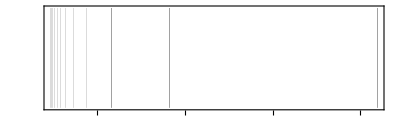

```mathematica
ElementAbsorptionMap[H]
```

```mathematica
WavelengthAbsorptionMap[5000 Angstrom, 7000Angstrom]
```

### System variables

Names beginning with the "$" character are called system variables.  Mathematica relies on their values to perform important tasks that are normally invisible to the user. We’ve already seen one in an earlier lab, the $Assumptions variable. Usually you won’t need to modify these, but situations might arise where you would want to.

```mathematica
Names["$*"]  (* here's a list of all the system variables *)
```

To see the current value of a system variable, just type in the variable name.

```mathematica
$ImportFormats   (* the available formats for the Import command *)
```

### Directory Navigation

In order to read in data from files, Mathematica has to know details about where the files exist. Same thing if you want to save data to a file. This is typically done by specifying a “working directory”, i.e. the location where all file reads/writes are steered. Some basic information is given in the tutorial on Naming and Finding Files. You can find more advanced info in the File Operations guide and the links found there.

These are two especially important directories:

```mathematica
$InitialDirectory   (* The initial working directory *)
Directory[]  (* The current working directory *)
```

You can set the working directory to be anywhere you like on the computer--just be careful, as the backslash character needs to be entered as a forward slash (or two backslash characters together also seem to work. Nice of Mathematica’s help file to mention either of those... NOT).

```mathematica
(* first change the directory location to one that exists on your computer *)
SetDirectory["/Users/dave/projects"]  ; 
Directory[]
SetDirectory["../"]     (* To go "up" a directory *)
```

Here we set the working directory back to the default $InitialDirectory and use FileNames to view the files in the current directory.

```mathematica
SetDirectory[$InitialDirectory];
FileNames[]
```

It would make a lot of sense if when you start Mathematica by double-clicking a notebook file, the working directory would automatically be set to the directory containing that file. However, that isn’t the case. Therefore here is a helpful shortcut to do that for you. I recommend you use it at the top of all of your workbooks from now on.

```mathematica
SetDirectory[NotebookDirectory[]]   (* This is EXTREMELY helpful!!! I use it all the time!! *)
```

### File Copy & Delete

Mathematica can copy and delete files using the operating system on your computer. To demonstrate that, first evaluate this cell to create a file in your working directory called "oldtest.txt".  Check to make sure that it was created.

```mathematica
Export["oldtest.txt",{1,2,3,4,5}]
```

oldtest.txt

Here’s how you would copy "oldtest.txt" to a new file called "newtest.txt".  Check to make sure that it was copied.

```mathematica
CopyFile["oldtest.txt","newtest.txt"]
```

C:\Users\carte\OneDrive\Documents\Wolfram Mathematica\newtest.txt

Here’s how to delete both files.  Check to make sure that they were deleted.

```mathematica
DeleteFile[{"oldtest.txt","newtest.txt"}]
```

## Data Import/Export/Processing

### Import/export of expressions

Begin by watching this short video about importing/exporting data.

Importing and exporting complete Mathematica expressions is really easy. You can browse the tutorial page on Reading and Writing Wolfram System Files for lots of information.

The bottom line is that just as Packages can be imported via the  << (Get) command, so can your own Mathematica expressions be imported via  <<  and exported via  >> (Put). The shortcuts are very intuitive, as can hopefully be seen by these examples.

```mathematica
Expand[(a+b)^10]
% >> "test.txt"    (*  this stores the expression in a text file called test.txt *)
```

a^10+10 a^9 b+45 a^8 b^2+120 a^7 b^3+210 a^6 b^4+252 a^5 b^5+210 a^4 b^6+120 a^3 b^7+45 a^2 b^8+10 a b^9+b^10

You should manually open the “text.txt” file in a text editor such as Notepad or Notepad++ (a great free program which is installed on all departmental lab computers) to see what the saved expression looks like. You can also view the contents of the file via Mathematica's FilePrint function:

```mathematica
FilePrint["test.txt"]
```

a^10 + 10*a^9*b + 45*a^8*b^2 + 120*a^7*b^3 + 210*a^6*b^4 + 252*a^5*b^5 + 
 210*a^4*b^6 + 120*a^3*b^7 + 45*a^2*b^8 + 10*a*b^9 + b^10

To read the information back in, you just need to use  <<.

```mathematica
expansion = <<"test.txt"
```

a^10+10 a^9 b+45 a^8 b^2+120 a^7 b^3+210 a^6 b^4+252 a^5 b^5+210 a^4 b^6+120 a^3 b^7+45 a^2 b^8+10 a b^9+b^10

### Importing numerical data

Mathematica supports many formats for Importing and Exporting data. In this section we’ll talk about numerical data. Later in this lab we’ll get to some other data types such as images and audio.

Import review.  We’ve already used the Import function once to grab data from a file, back in Lab 2 when we were discussing lists. Let’s revisit that. Download the file Th000088.txt again (it contains reflectance data) and put it into the directory where you have saved this notebook.

Before proceeding with these next commands, which will create an array called “tdata” and fill it with the data, look at the data file itself with a text editor such as Notepad++. It’s a very common type of data file--a row of header information, followed by the raw data. Each row of data begins with one independent variable value (wavelength in nm), then has several dependent variables. The numbers within each row are separated by tabs.

OK, here’s the command used in Lab 2 to read in the data. Notice the “Table” option that is used. That tells Mathematica that it will be dealing with a “tab-delimited” text file (i.e. numbers separated by tabs).

```mathematica
SetDirectory[NotebookDirectory[]]
tdata = Import["Th000088.txt","Table"]
```

C:\Users\carte\Downloads

Import::nffil: File Th000088.txt not found during Import.

$Failed

The Lab 2 exercise involved you manipulating the list--you needed to drop the first row of data, extract the wavelength & reflectance data as pairs of numbers, then plot them using ListLogPlot. Here are the commands I myself used to accomplish that. Make sure you understand how/why all of my commands work (your own commands for that assignment likely did things slightly differently).

```mathematica
ourdata=Drop[tdata,1];   (* I've defined "ourdata" so I can refer to it below. It's not needed for this task. *)
Transpose[%];  
Drop[%,-2];
xydata = Transpose[%]
ListLogPlot[xydata]
```

A trick worth knowing.  In my commands above, the first Transpose followed by the Drop[%,-2] command served to drop the final two columns. Probably most of you did something similar to that, but here’s another neat way of doing the same thing. First, observe what ourdata //Transpose looks like:

```mathematica
ourdata //Transpose   (* it's a collection of four separate lists *)
```

Here’s the trick:

```mathematica
{wavelength, reflect, garbage1, garbage2} =  ourdata  //Transpose ;     (* look at the left hand side of the equals... this is slick! *)
newxydata= {wavelength, reflect} //Transpose
```

Things to notice: 
ourdata // Transpose is a collection of four lists--two that we care about, and two that we don’t.  By writing the left hand side of the first command as  {wavelength, reflect, garbage1, garbage2} , I’ve automatically defined “wavelength” to be the first of those four and “reflect” to be the second. Then I can deal with them however I want. Defining distinct parts of arrays like that is very slick and can be very useful when reading in files.

### Exporting numerical data

Let’s suppose now that you wish to re-save the data into a new file, but just the wavelength and reflectivity numbers that are now in the “xydata” array and not the header row or other two columns that were part of the original tdata array.

The Export command has a nice  “Table” format specifier just like the Import command had. The “Table” format uses tabs to delimit (i.e. separate) the columns in the output file, though options are available for using other delimiters such as commas or spaces.

#### Assignment 1. Exporting data

(a) View the xydata array in TableForm to see what it will look like in a file if you use the Table format specifier.
(b) Now Export the xydata array to a file in your working directory named "xydata.txt" using the Table format. (Note that if you were to use a filename with a ".dat" extension, "Table" would be the default format and would not need to be specified.)  View the xydata.txt file to make sure things worked as expected.
(c) Another very common input/output format is the csv or “comma separated variables” format. That format uses comma to separate the data on each line. Mathematica is smart enough that simply by giving the filename a “.csv” extension, it will automatically save the data with commas. Export your xydata array to a file called “xydata.csv” and use a text editor to verify that you now have commas where the xydata.txt file had tabs. (As an added bonus, csv files can typically be opened as spreadsheets in Microsoft Excel by simply double-clicking the file in Windows Explorer.)

### Interpolating functions

Sometimes you may want the data you have imported to be able to be treated just like a regular function. For those times, the Interpolation function is handy. It allows you to take a list of values (e.g. {x,y} pairs) and define a function based on them. Then you can evaluate the function at any point and it will interplote a value based on the data you supplied. You can even use it in a regular Plot command instead of needing to do a ListPlot.

```mathematica
xyfunction=Interpolation[xydata]  (* Values between the data points are now interpolated. *)
xyfunction[200.5]  (* This point doesn't exist in the original data, but it exists now. *)
Plot[xyfunction[x],{x,172,250}]  (* Using Plot instead of ListPlot. *)
```

### Formatting output

When you did Assignment 1 above, the output file  xydata.txt  probably had nice, clean columns of data inside of it. However, Mathematica sometimes has issues in this regard. Consider this new set of data which I’ve called “morexydata” (it’s a noisy parabola).

```mathematica
morexydata= Table[{n,n^2+5*RandomReal[{-1,1}]}, {n,0,10,0.2}];
% //TableForm
```

It looks like a nice, clean, table of data, so let’s save it to "morexydata.txt" using our standard method.

```mathematica
Export["morexydata.txt",morexydata,"Table"]
```

Now open up  morexydata.txt  with a textedit and look at what actually got saved.  Ugly!!   Not only is the second column adding a bunch of unwanted decimal places, the first column is also messed up, apparently because there’s a very small rounding error that occurs when the Table command generates the multiples of 0.2.

There are various ways you can deal with this type of situation. Here’s a method that involves converting numerical data into nicely formatted strings prior to export.

```mathematica
niceoutput = Map[ToString[NumberForm[#,{10,6},NumberPadding->{" ","0"}]]&,morexydata,{2}]
Export["morexydata2.txt",niceoutput,"Table"]
```

Open the morexydata2.txt file in an external text editor to verify the results. Much nicer!

Now change the values above in {10, 6} and {“ “, “0”} to see what they do.

## Short Detour: Strings

### String basics

That last example involved translating your number into a formatted string. A String is a variable type in Mathematica, just like an integer, real number, complex number, Boolean, etc. We’ve used strings before--they are just text characters grouped together via surrounding quotation marks--but we haven’t really stopped to talk about them. Just as numbers and Booleans have a lot of built-in functions for manipulating them, so do strings. We could probably spend an entire lab just on string functions, so we’ll have to stick to the basics here.

Numbers can be transformed into strings, and strings that look like numbers can be transformed into numbers. ToString and ToExpression are the commands.

```mathematica
thisisanumber = 12345
thisisanumber + 5
thisisastring=ToString[thisisanumber]  (* this is NOT a number. thisisastring is a string that LOOKS like a number *)
thisisastring +  5   (* addition doesn't work because thisisastring is not a number *)
```

```mathematica
anotherstring = "2468"  (* this is NOT a number *)
anotherstring + 5  (* this isn't going to work *)
anothernumber = ToExpression[anotherstring]  (* NOW this is a number *)
anothernumber + 5
```

The ToExpression command works on strings that look like any expressions (algebraic, etc.), not just on strings that look like numbers:

```mathematica
zstring = "-1 + 3 x + x^2"   (* this is a string, NOT an expression... *)
Plot[zstring,{x, -3,3}]  (* ... and so this will not work at all *)
```

```mathematica
zexpression = ToExpression[zstring]  (* this converts the "x^2 + 3*x - 1" string into a real expression... *)  
Plot[zexpression,{x, -3,3}]   (* ... and so this WILL work *)
```

In some sense, a string is like a list of single characters. Therefore a lot of things that we’ve done with lists can be done with strings using string versions of the commands: reversing, inserting, replacing, etc. Many of the string-specific functions can be found in these two guides: String Operations and String Manipulations.

Some quick demonstrations:

```mathematica
sentence = "This is " <> "a sentence."   (* <>  is shortcut notation for StringJoin, which acts like Append does for arrays *)
StringLength[sentence]   (* how many characters *)
StringReverse[sentence]
StringInsert[sentence, "very cool ",11]
StringReplace[sentence, "is" -> "zzz"]
StringPosition[%, "zzz"]  (* where are the zzz's? Gives first and last index for each found string *)
StringPosition[%%, "zzz", 1]  (* just the first zzz *)
Sort[{"This", "is", "a", "list"}]  (* Sort puts string array elements in alphabetical order *)
```

### Merging numbers into a string

Often you may want to merge one or more numbers into a string, perhaps when (for example) displaying the result of a calculation. There are two fairly easy methods:
1. You can convert the numbers into strings, then use  <>   (StringJoin)
2. You can use StringForm, followed by a set of numbers. Each number that is to be merged into the string is given the symbol  ``  in the string as a temporary placeholder.

```mathematica
number1 = E^1.5
number2 = Log[1.5]
sentence1 = "The exponential was " <>  ToString[number1] <> " and the natural log was " <>  ToString[number2] <>"."
sentence2 = StringForm["The exponential was `` and the natural log was ``.", number1, number2]
```

StringForm can be combined with NumberForm to specify how many significant digits of the numbers should be displayed.

```mathematica
sentence2 = StringForm["The exponential was `` and the natural log was ``.",NumberForm[number1, 9], NumberForm[number2,8]  ]
```

Incidentally, the StringForm command works with other things too, not just numbers.

```mathematica
StringForm["Performing the integral `` results in ``.",HoldForm[Integrate[x^2,x]],Integrate[x^2,x]]
(* HoldForm means it shouldn't do the integral yet *)
```

### Converting strings to lists

Although a lot of the list functions have string analogs, sometimes they don't. For example, I was once unable to find a string analog to the PadLeft list function when I wanted to display a list of integers with leading zeroes. I was able to do it by creating a function which converts a number to a string, then converts the string to a list of characters (using Characters), then applies PadLeft to the list, then does a StringJoin to convert the list of characters back into a single string.

```mathematica
fixedwidth[num_Integer]:= StringJoin[
PadLeft[Characters[ToString[num]],8,"0"]    (* adds array elements of 0's on left so array has 8 elements in it *)
]
Do[Print[fixedwidth[i]],{i,1,15}]
```

#### Assignment 2. A string function

Create a function using Module which takes two arguments: an expression containing x and a numerical value to plug in for x, then prints out the phrase “The value of <expression> when x = <number> is: <the answer>”.

### Import of string (text) data

In the previous section we imported some undesired numerical data as a string, so we could throw it out. However, sometimes you may be dealing with data that is actually in string (text) format. For those cases, the tutorial on Reading Textual Data may be helpful.

To set up this example, download the “funwithstring.txt” file from the course website into your working directory. Before running the commands in the next box, look at the file with a text editor so you know what you’re dealing with. Then use these commands to Import it into a list called firsttry (assuming a “Table” format) and examine it using TableForm.

```mathematica
firsttry= Import["funwithstring.txt","Table"];
firsttry//TableForm
```

The innocent-looking data has actually not imported well at all. The main issue is that some of the names got imported as last & first columns, whereas others got imported into last & first & middle initial. Therefore some rows have 8 elements and some have 9. And to add insult to injury, one of the street names was “North Hitchcock Way”, so , it got imported into three separate column elements instead of two columns like the other street names (because the table import assumed all elements were separated by spaces). 

To solve this problem, after I noticed that the data was all separated by commas I just manually renamed the file to “funwithstring.csv”. Do that now, yourself. Then you can use import with no additional specifiers, and no issues.

IMPORTANT: Depending on what options you have in place with Windows, you might not be able to change the file extension (the “.txt” or “.csv”). The default behavior of Windows is to not allow people to change file extensions, so if it looks like you renamed the file to “funwithstring.csv” but it still shows up as a text file, you undoubtedly really renamed the file to “funwithstring.csv.txt”. To change the default behavior in Windows, when in Windows Explorer press Alt-v to get to the View tab, then check the box that says “File name extensions”. Then you will be able to see and modify the file extension.

```mathematica
secondtry= Import["funwithstring.csv"];
secondtry//TableForm
```

As another way around the issue, you could also import the data using the {"Text","Lines"} specifier. That reads in each line as its own string, giving you an array of strings that represents the file contents.

```mathematica
thirdtry = Import["funwithstring.txt",{"Text","Lines"}]   
%//InputForm   (* InputForm shows you where the quotation marks are *)
```

```mathematica
(StringSplit[#,", "]&)/@thirdtry   (* manually splitting each string at the commas *)
```

```mathematica
% //TableForm  (* to see things in a nicely formatted table *)
```

## Multimedia

Multimedia files involving images, audio and/or video, have become important methods to record, store, share, and visualize scienfic data. Mathematica supports a large number of Import/Export formats.  The Import and Export reference pages are fairly limited, but contain links to a number of good tutorials. You can also view the complete list of supported formats, grouped by media type or grouped alphabetically, to learn about the special options available to individual formats.  As in the “csv” examples above, if you give your filemame a common extension (such as “.jpg” in this context), Mathematica should automatically figure out how to deal with that particular format. Otherwise, you can provide a format specifier (e.g. "JPEG") as an argument to Import or Export.

### Loading data from “Example Data”

Mathematica has a lot of miscellaneous data that can be used for testing purposes, called ExampleData. Here’s a list of all of the categories.

```mathematica
ExampleData[]
```

You can also list all of the data available within a particular category. Here’s all of the data in the “test image” category.

```mathematica
ExampleData["TestImage"]
```

To view/access one of those test images, you use the ExampleData function like this:

```mathematica
colorpeppers = ExampleData[{"TestImage","Peppers"}]
```

### Loading data from internet

In addition to loading images that are in the ExampleData, one can also Import images from disk or from the internet, just like you would load numerical data files. For example, here’s a picture I took of the Nauvoo temple:

```mathematica
temple = Import["http://www.physics.byu.edu/faculty/colton/personal/lds/temple1.jpg"]
```

### Images

The data involved in producing an image is stored as a 2D array of pixels. Each pixel can contain either one number or a triplet of numbers in a list. If a single number exists, Mathematica will interpret the data as a black and white image. If a triplet exists, it will be a color image, with the three numbers indicating how much red, green, and blue there is in the pixel. The Image command causes the pixel information to be displayed as a picture. Here are some examples, but just using random numbers so that the “picture” doesn’t actually look like anything.

```mathematica
bwarray=RandomReal[{0,1},{20,10}];  (* a 20x10 array of random numbers between 0 and 1 *)
%//MatrixForm
```

```mathematica
Image[bwarray]  (* a black & white (grayscale) image of the random data, 20 rows and 10 columns of pixels. 
You can enlarge the image by clicking on the image and then dragging on a corner. Make it big enough that you can see the individual pixels. *)
```

```mathematica
colorarray=RandomReal[{0,1},{20,10,3}];  (* a 20x10 array of pixels, each pixel now being a 3 element list *)
%//MatrixForm
```

```mathematica
Image[colorarray]  (* This now produces a color image, because Mathematica recognizes that there's a list of three numbers given for each pixel *)
```

You can access individual pixels using the regular list commands.

```mathematica
bwarray[[1,1]]  (* current value of upper left pixel *)
bwarray[[1,1]]=1  (* sets upper left pixel to pure white; click and drag the corner of image to enlarge it and verify that *)
Image[bwarray]
```

```mathematica
colorarray[[1,1]]  (* upper left pixel *)
colorarray[[1,1]]={1,0,0}  (* sets upper left pixel to pure red; enlarge image to see it *)
Image[colorarray]
```

Metadata. In addition to the numbers which make up the pixels, some “metadata” is also often stored in the image which can include information about how the numerical data is to be used, where the picture was taken, and so forth. You can see the metadata in the peppers image, for example, by removing the semicolon in the next cell, then evaluating it. There’s a dizzying amount of numbers, but then at the end of the numerical data you can see:  “Byte”, ColorSpace -> “RGB”, Interleaving -> True. That’s the metadata. (I recommend you delete the lengthy output when you are done looking at it so it doesn’t clutter up your notebook.)

```mathematica
colorpeppers//InputForm;  (* remove semicolon to see output *)
```

You can access the pixel information in a pure numerical list format via the ImageData command:

```mathematica
colorpeppersdata = colorpeppers//ImageData; 
colorpeppersdata[[1;;3]]  //TableForm  (* the first three rows of pixels *)
```

#### Assignment 3. Black and white peppers

The goal of this problem is to produce a black and white peppers image based on the color image of the peppers seen above. Part (a) is an easier version of the problem, then part (b) applies the same technique to the peppers image itself. 

(a) Working with your colorarray data from above, figure out how to replace each pixel, i.e. each three element list, with a single number that is the average of the three values. Use the Map command, which we often shortcut as  /@.  

Hint: You cannot actually easily use the shortcut notation in this case, because the default behavior of Map (and  /@ ) is to perform an operation on each row of the matrix. We need to perform an operation (i.e. average the numbers) on each pixel in the matrix. Using Map with a  {2}  for the “levelspec” argument will do this. (Look at the help file to see where that goes.) You will know that you have succeeded when you can view the result in MatrixForm, and see a 20x10 list of numbers (rather than a 20x10 list of triplets).  And when you have done that, you will be able to use Image to see a black and white version of your colorarray data.

(b) Now use the same technique on colorpeppersdata. This creates a black and white equivalent of the original color image of the peppers. View it with Image to verify the result, then Export the grayscale image to a “.jpg” file and open that file with external software.

### Video

Mathematica can import and export a number of video formats, including AVI, FLV (Flash video), QuickTime, and animated GIF. The guide page on Multimedia Formats contains links to information on many of them. For this lab, we’ll focus on the single task of exporting animations to a video format which you might want to embed in a presentation or display on the web.

Exporting with Animate. Perhaps the simplest way to export data is to create an animation with Animate, then use the Export command. You can export to AVI, MOV, or SWF formats in this way (and probably others). AVI files are the largest but most universally accepted by programs such as PowerPoint.  MOV format files are much smaller and faster if your target software supports them.  SWF files are also much smaller and work well on web pages. 

Let’s create an animation of a traveling sine wave. (Try the Background-> White version if you have any issues with flickering.)

```mathematica
sinewave = Animate[Plot[Sin[2 Pi (x-t)],{x,0,2}], {t,0,2}]
(* sinewave = Animate[Plot[Sin[2 Pi (x-t)],{x,0,2},Background->White], {t,0,2}] *)
```

Here’s how you would store the animation as an AVI file. (This takes a bit of time, ~25 seconds on my fairly fast office computer.)

```mathematica
SetDirectory[NotebookDirectory[]]
Export["sine.avi",sinewave]
```

Verify that it worked by viewing the file using something like Windows Media Player or VLC Media Player. Some things might catch you by surprise, such as (a) the animation includes the (non-functioning) controls, and (b) the animation runs forward and then backward, instead of just forward.

Exporting by creating an array of images.  Although using the Animate command followed by Export is often the simplest way to export a video, it is not usually the best way. In fact, I myself never use it. A better way to create animations is to create an array of graphics objects and then export the array. That usually provides a smoother animation, a smaller file, and removes the two oddities mentioned in the last paragraph.

The next cell creates 41 different graphs (from t = 0 to t = 2, in steps of 0.05), then exports them into a single, merged avi file. Verify that the file sine2.avi gets created, and is viewable in e.g. Windows Media Player. (This takes far less time than the sine.avi animation done previously.)

```mathematica
sineWaveArray=Table[Plot[Sin[2 Pi(x-t)],{x,0,2}],{t,0,2,0.05}];
Export["sine2.avi",sineWaveArray, AnimationRate->10]
```

#### Assignment 4. Exporting an animation

Export an animated gif (save it to the notebook directory as “filename.gif”) of the function f(x,y,t)=3 cos(0.2 t) exp(-1/3 (x^2+y^2)) for x and y between -5 and 5, and t going from 0 to 20π (in steps of 0.5). Use Plot3D to display the function. Use PlotRange->{All, All, {-3,3}}  as a plot option in order to preserve the z-axis scale from plot to plot.

### Audio

Mathematica can represent functions not only as graphs via the Plot command, but also as sounds via the Play command. Listen to the output of Play in this example (use headphones if your computer doesn’t have speakers; you can borrow a pair from a TA or a fellow student if you don’t have your own).

```mathematica
concertA[t_] = Sin[2 Pi 440  t]  (* t assumed to be in seconds *)
Plot[concertA[t],{t,0,.05}]
Play[concertA[t],{t,0,2}]
```

Here’s a dial tone for you:

```mathematica
dialtone[t_] = Sin[2 Pi 440  t] + Sin[2 Pi 350 t]
Play[dialtone[t],{t,0,2}]
```

Sounds are elements of the Sound category. Play is only the most basic sound-related command. The guide page on Sound and Sonification contains links to most of the additional standard functions for creating and analyzing audio signals. If you have have a strong interest in music and/or audio, you may also want to explore the special Music and Audio packages. 

Here’s another example. This is just for fun, but why would a constantly increasing frequency sound like it does when Mathematica plays it?

```mathematica
expfreq[t_]=Sin[2 Pi 440 Exp[t]]
Play[expfreq[t],{t,0,6}]
```

As with numerical data and image data, one can Import audio data from disk or from the internet, and there are also many audio clips available via ExampleData.

#### Assignment 5. Deepening a French horn

(a) Find and load the FrenchHorn example data listed under “Sound”. Play the sound (the Play command is not even needed). Use InputForm to look at the metadata at the end of the list of numbers (delete after done viewing). There should be only a single item of metadata: the number 22050. That indicates the sampling rate (in Hz). It’s at the [[1,2]] position of the data, as you should be able to verify.
(b) Modify the horn sound by replacing the number 22050 with the number 11025. What happens to the horn sound, and why? (There are two effects.) 
(c) Export the new sound as a wav file, and verify that it plays in e.g. Windows Media Player.

## Integrated Data Sources

A cool feature of Mathematica is its ability to interact with Wolfram’s collection of “curated data”. The curated data sets give you access to values from chemistry, astronomy, geography, the stock market, etc., and are actively updated by Wolfram’s staff as new/better values become available. See this website for a partial listing of available data sources: https://www.wolfram.com/technology/guide/LoadOnDemandCuratedData/  

The data sets are accessible in real-time over the internet without needing to specify any webpages or anything like that. Whenever you query one of the data sources, the requested data is automatically downloaded to your computer and imported into your notebook. While we only have time to explore two of the available data sources in this section, you are encouraged to explore some of the others later on your own.

### Element Data

ElementData provides a variety of information on each element in the periodic table.  Evaluate the cell below, where we display a list of the elements in the database and a list of the properties that may be available for each element.

```mathematica
ElementData[]
properties = ElementData["Properties"]
```

To access a particular property, you just use the ElementData function, specifying the material and the property. For example, here are the atomic number and density of iron (in SI units).

```mathematica
ElementData["Iron","AtomicNumber"]
ElementData["Iron","Density"]
LinguisticAssistant  (* for this one I typed "<control-equals>density of iron" *)
```

Here’s a command to see all of the information on iron, all at once. It produces lengthy output so I recommend running the command in a new window.

```mathematica
MatrixForm/@{#,ElementData["Iron",#]}& /@ properties // TableForm; (* remove semicolon to display output *)
```

Not every property has been measured for every element in the periodic table.  You probably saw that some of the properties of iron were listed as Missing because they were either "NotAvailable", "NotApplicable", or "Unknown".  Here’s a function that will be useful to you--it eliminates any Missing items from a list of data.  We test it for one example to display all of the elements whose magnetic and electrical types are known.

```mathematica
skipmissing[data_] := Select[data,!MemberQ[Flatten[#],_Missing]&]

{#,ElementData[#,"MagneticType"],ElementData[#,"ElectricalType"]}&  /@ ElementData[];
% // skipmissing
```

#### Assignment 6. Melting and boiling points

(a) Create a 2D list that contains a pair of Kelvin-degree temperatures, the "AbsoluteMeltingPoint" and the "AbsoluteBoilingPoint", for each element in the database. (No need to have the element name in the list.) Then use skipmissing to eliminate the pairs that are Missing one or both of these temperatures, and employ N to ensure that all of the entries contain true floating-point data.
(b) ListPlot the resulting data with the following options:  PlotRange → All, Frame → True, FrameLabel → {“Melting Point (K)”, “Boiling Point (K)”}.  What do you learn from this plot?

### Astronomical Data

Evaluate the cell below to learn more about the information available through AstronomicalData.  The four commands display the total number of astronomical objects in the database, the object classifications used (e.g. planet, moon, star, galaxy, etc.), the properties stored for these objects, and finally an image of each “Planet” in our solar system (sorry, Pluto!).

```mathematica
Length[AstronomicalData[]]
AstronomicalData["Groups"]
properties =AstronomicalData["Properties"]
{#,AstronomicalData[#,"Image"]}& /@  AstronomicalData["Planet"]
```

#### Assignment 7. Hubble’s Law

(a) Create a 2D list called data1 that contains pairs of numbers: the “DistanceLightYears” and the “Redshift”, for every "Galaxy" in the AstronomicalData database (supress the output; it’s long).  Then use skipmissing to eliminate the pairs that are Missing one or both of these quantities, and employ N to ensure that all of the entries contain true floating-point data.  Name the result data1.  Once you have succeeded, suppress the lengthy output with a semicolon. Hint: Be sure to select for galaxies the same way I selected for planets in the example above. To check yourself, there were 729 useable galaxies in the curated data as of Jan 2014.

(b) The distances in data1 are measured in light years and the redshifts are unitless.  A more traditional description would express the distances in megaparsecs, and would multiply the unitless redshifts by the speed of light in kilometers per second.  We provide multiplicative conversion factors in the cell below.  Convert data1 to traditional units and name the result data2. Then ListPlot data2. You should find a nearly linear relationship between how far away a galaxy is (the x-axis, the distance in megaparsecs), and how fast it’s traveling (the y-axis, the redshift in km/s). That is Hubble’s Law, discovered by Edwin Hubble in 1929, and is strong evidence for the Big Bang theory (the scientific model, not the TV show). The slope of the line indicates the rate of the expansion of the universe. 

Hint: One way to apply the conversion factors is to make a nameless function that multiplies the first element of a pair by mpperly and the 2nd element of a pair by lightspeed, and then use /@ to evaluate this function for each element in data1. Alternatively, you could separate data1 into two lists with Transpose, multiply each list by the appropriate constant, then re-form your x-y pairs with a second Transpose command.

```mathematica
mpperly = 3.0660*^-7; (* Megaparsecs/LightYear *)
lightspeed = 2.9979*10^5; (* km/sec *)
```

## Additional Assignments

#### Assignment 8. Calibrating spin resonance data

(a) The file spinres.csv, available on the Physics 230 website, contains data from an electron spin resonance experiment I did where the magnetic field was changed while we recorded an optical signal measuring electron spin polarization. The first column represents the magnetic field as recorded by a magnetic field sensor; the second column is the optical signal. Read in the file and ListPlot the data. Be sure to use the PlotRange->All option. Hint: since it’s in a nice csv format, you can read the data in with a simple Import comand without any options.
(b) The y-axis scale isn’t too important, but the x-axis scale is critical. The problem here is that the x-axis is not really displaying magnetic field (which should range from 0.718 to 0.841 T), it’s displaying the voltage from my field sensor (which ranged from -1.207 to -1.157 V). We need to therefore convert the magnetic field sensor data into tesla and replot. In a separate experiment, I calibrated the magnetic field sensor so I would know what voltage from the sensor corresponded to what field. The calibration information is in in a file called calibration.csv; the first column is voltage and the second column is the field (in tesla) that a given voltage corresponded to. Read in the calibration information, use it to define a calibrating function (via Interpolation), and use that to change your x-values into tesla. Then make a ListPlot of the optical signal vs. actual field in tesla. This plot should look like a reversed version of the first plot, but with the proper magnetic field range (0.718 - 0.841 T) along the x-axis.

## Wrap-up

The following functions were discussed in today's lab, or are very closely related:

See all Mathematica functions: Names 
Load package: Get (shortcut <<), or  Needs 
Packages: Units  (with Convert, SI, and CGS commands),  Physical Constants 
Directory/file-related commands: $InitialDirectory, Directory, SetDirectory, FileNames, CopyFile, DeleteFile, FilePrint 
Import/export of expressions:  << (Get) and  >> (Put)
Import/export of data:  Import, Export, ReadList, Read
Creating a function from a set of {x,y} pairs: Interpolation 
Viewing data in a table: TableForm
Viewing strings with quotes around them, or image/sound data in numerical format (with metadata): InputForm
String conversions: ToString (number or expression to string), ToExpression (string to number or expression), Characters (string to list of individual characters)
String functions: String, StringLength, StringReverse, StringInsert, StringReplace, StringPosition,  <> (StringJoin), StringSplit 
Merging numbers into strings: StringForm (often with NumberForm)
Input streams: OpenRead, Skip, ReadList, Close
Data for testing:  ExampleData
Image functions: ImageData 
Audio functions: Play, Sound 
Misc array function: PadLeft, ReplacePart 
Two of the integrated data sources: ElementData, AstronomicalData


Potentially useful summary/tutorial pages: 

Guide: File Operations
Tutorial: Units Overview
Tutorial: Reading and Writing Wolfram System Files 
Tutorial: Naming and Finding Files
Guide: Importing and Exporting data
Guide: String Operations 
Guide: String Manipulations
Tutorial: Reading Textual Data
Guide: Listing Of All Formats
Guide: Multimedia Formats 
Guide:Sound and Sonification 
Guides: Music and Audio packages
Wolfram website on curated data: https://www.wolfram.com/technology/guide/LoadOnDemandCuratedData/